## Import

```mathematica
Clear["Global`*"]
SetDirectory["C:/Users/npnik/Documents/Project/Codes"];
importedMats=Import["matricesInvPend.mat","Data"];
SetDirectory["C:/Users/npnik/Documents/Project/Codes/Packages"];
<<"costfunc`"
<<"spectralMPC`"
```

## Constants

```mathematica
hor=12; (*optimisation horizon*)
ExtHor=5;
NetHor=hor+2*ExtHor;
γ=1/10;
α=1/10;
β=1/10;
ConstraintRelaxer=1;
T=150; (*simulation samples of time*)
iters=10;
		
A=importedMats[[1]];(*matrix*)
B=importedMats[[3]]; (*matrix*)
Cw=importedMats[[4]];
Cout={{1,0,0,0},{0,0,1,0}}; (*matrix. output-state state space matrix.*)
Dout=importedMats[[5]];  (*matrix. output-input state space matrix.*)
n=Dimensions[A][[1]]; (*dim of state vector*)
m=Dimensions[B][[2]]; (*dim of input vector*)
nw=Dimensions[Cw][[2]];
o=Dimensions[Cout][[1]]; (*dim of output vector*)

Q=importedMats[[6]]/10;(*matrix. state cost.*)
R=1;(*matrix. input cost. scalar if control action is scalar*)
sstr=StateSpaceModel[{A,B,Cout,Dout},SamplingPeriod->1/10];
K=LQRegulatorGains[sstr,{Q,{{R}}}];
Qf=(DiscreteLyapunovSolve[Transpose[A-B.K],-(Q+Transpose[K].{{R}}.K)])(*importedMats[[5]]*);(*matrix. terminal cost.*)

ic={0,0,45/1000,0};(*list. initial state vector.*)
oldOutputs=Flatten[ConstantArray[0,{ExtHor,o}]];
oldCtrlActions=Flatten[ConstantArray[0,{ExtHor,m}]];
ExtendedA=A-B.K;

lengthOfFlattenedNoiseVector=hor*nw*(hor*m+1);
```

## Requisite function definitions

```mathematica
om[ID_,NetHor_]:=Piecewise[{{Exp[-I 2Pi/NetHor+ID],ID==0},{Exp[-I 2Pi/(NetHor+1)+ID-ID],ID==1}}];
BlkDiag[M_,num_]:=Fold[ArrayFlatten[{{#,0},{0,#2}}]&,M,ConstantArray[M,num-1]];
usefulFunction[ID_]:=Piecewise[{{0+ID,ID==0},{0+ID*0,ID==1},{-1+ID*0,ID==2}}];
Cost=Compile[{{x,_Real}},countt=countt+1;x,"RuntimeOptions"->"EvaluateSymbolically"->False];

penalty=Compile[{{slackVar,_Real}},PenaltyCoefficient*Max[0,-slackVar],"RuntimeOptions"->"EvaluateSymbolically"->False];
```

#### ℱ and its analogues

```mathematica
ℱs[ID_,NetHor_]:=1/Sqrt[NetHor+ID+usefulFunction[ID]]*Table[om[ID+usefulFunction[ID],NetHor]^((i-1)*(j-1)),{i,NetHor+ID+usefulFunction[ID]},{j,NetHor+ID+usefulFunction[ID]}];
ℱ[ID_,NetHor_]:=Fold[ArrayFlatten[{{#,0},{0,#2}}]&,ℱs[ID,NetHor],ConstantArray[ℱs[ID,NetHor],whatdim[ID]-1]];
```

#### Permutation matrices

```mathematica
whatdim[ID_]=Piecewise[{{m+ID,ID==0},{n+ID*0,ID==1},{o+ID*0,ID==2}}];
ListPs[ID_,NetHor_]:=Table[ArrayFlatten[Fold[ArrayFlatten[{{#},{#2}}]&,UnitVector[whatdim[ID]*(NetHor+ID+usefulFunction[ID]),i],Table[UnitVector[whatdim[ID]*(NetHor+ID+usefulFunction[ID]),i+k*(NetHor+ID+usefulFunction[ID])],{k,whatdim[ID]-1}]],1],{i,NetHor+ID+usefulFunction[ID]}];
Perm[ID_,NetHor_]:=If[whatdim[ID]==1,ListPs[ID,NetHor],Fold[ArrayFlatten[{{#},{#2}}]&,ListPs[ID,NetHor][[1]],ListPs[ID,NetHor][[2;;NetHor+ID+usefulFunction[ID]]]]];
```

#### Domain transforming matrices

```mathematica
Ts[p_,ID_,NetHor_]:=Array[om[ID,NetHor]^(-p*(#-1))&,NetHor+ID];
f[i_,const_,ID_,NetHor_]:=Block[{row},row=ConstantArray[0,whatdim[ID]*(NetHor+ID)];
row[[(i-1)*(NetHor+ID)+1;;i*(NetHor+ID)]]=const;
row];
Trans[p_,ID_,NetHor_]:=1/Sqrt[NetHor+ID]*(f[#,Ts[p,ID],ID,NetHor]&/@Range[whatdim[ID]]);
f1[i_,ID_,NetHor_]:=Module[{mat},If[Mod[i,whatdim[ID]]==0,mat=Trans[Ceiling[i/whatdim[ID]],ID,NetHor][[whatdim[ID]]],mat=Trans[Ceiling[i/whatdim[ID]],ID,NetHor][[i-whatdim[ID]*Floor[i/whatdim[ID]]]]];mat];
BigTrans[ID_,NetHor_]:=Table[f1[i,ID,NetHor],{i,whatdim[ID]*NetHor}];
```

## Matrices needed in optimization problem

```mathematica
S1=ConstantArray[0,{m,m*NetHor}];
(*S1={{0,0,0,0,1,0,0,0,0,0}};*)
S2=ConstantArray[0,{o,o*(NetHor+1)}];
(*S2={{0,1,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};*)
CtrlActionFreqConstraintMat=N[ArrayFlatten[{{S1.Re[ℱ[0,NetHor]]},{S1.Im[ℱ[0,NetHor]]}}].Inverse[Perm[0,NetHor]]];
OutputFreqConstraintMat=N[ArrayFlatten[{{S2.Re[ℱ[2,NetHor]]},{S2.Im[ℱ[2,NetHor]]}}].Inverse[Perm[2,NetHor]]];
XPolytope=ArrayFlatten[{{IdentityMatrix[n]},{-IdentityMatrix[n]}}];
```

## Optimization Pre-processing

```mathematica
flattenedCtrlActions=Table[Unique["u"],{hor*m}];
CtrlActions=Table[flattenedCtrlActions[[i;;i+m-1]],{i,1,(hor*m)-m+1,m}];(*just defined here for the case of non scalar u. in that case, this will need to replace flattenedCtrlActions everywhere along with some other minor changes elsewhere in the code.*)

(*flattenedStates=Table[Unique["x"],{(hor+1)*n}];
states=Table[flattenedStates[[i;;i+n-1]],{i,1,((hor+1)*n)-n+1,n}];*)
Su=Sumatrix[A,B,hor,n,m];
Sx=Sxmatrix[A,hor,n];
Sw=Sumatrix[A,Cw,hor,n,nw];
ExtendedSx=Sxmatrix[ExtendedA,ExtHor,n];
ExtendedSw=Sumatrix[ExtendedA,Cw,ExtHor,n,nw];
SubflattenedStates=Sx.ic+Su.flattenedCtrlActions;
```

## Relaxed OCP

```mathematica
relaxedOCP[ic_,flattenedNoiseVector_?(VectorQ[#, NumericQ] &)] :=
  
  Block[{ ControlObjective1, 
    setConstraints1, slackVar, NoiseVector, Constraints ={}, 
    stateDynamics, OutputFreqConstraint, OutputFreqConstraint1,copyVar,iCons},
   
  NoiseVector = 
    Partition[flattenedNoiseVector,hor*nw];
   (*states[[1]] = ic;
flattenedStates[[1;;n]]=ic;*)
 
   (*ControlObjective = Sum[states[[i]].Q.states[[i]] + flattenedCtrlActions[[i]]*R*flattenedCtrlActions[[i]],{i,1,hor}] + 
     states[[hor + 1]].Qf.states[[hor + 1]];*)(*objective function. 
   change the use of "*" instead of "." if u is non scalar.*)

  (* flattenedOutputs =Flatten[Map[Cout.#&,states]];*)

iCons = 
       Map[(-6*ConstraintRelaxer≤ # ≤ 6*ConstraintRelaxer)&, flattenedCtrlActions];

   (*SetSharedVariable[Constraints];Clear[doomplock];*)

   Do[
   (* SmallNoiseVector = NoiseVector[[i]];
    Noise = Partition[SmallNoiseVector, nw ];*)
    flattenedStates=SubflattenedStates+Sw.NoiseVector[[i]];
states=Partition[flattenedStates,n];
flattenedExtendedStates=ExtendedSx.states[[hor+1]]+ExtendedSw.RandomReal[γ,ExtHor*nw];
ExtendedStates=Partition[flattenedExtendedStates,n];
LongStates=Join[states[[1;;hor]],ExtendedStates];

flattenedExtCtrlActions=Flatten[Map[-K.#&,ExtendedStates[[1;;ExtHor]]]];
LongFlattenedCtrlActions=Join[oldCtrlActions,flattenedCtrlActions,flattenedExtCtrlActions];

 flattenedOutputs =Flatten[Map[Cout.#&,LongStates]];
LongFlattenedOutputs=Join[oldOutputs,flattenedOutputs];
    (*stateDynamics =
    Dispatch[ Table[Thread[states[[i]] -> 
     Flatten[(A.states[[i - 1]] + B*flattenedCtrlActions[[i - 1]] +
             Cw.{Noise[[i - 1]]})ᵀ]], {i, hor + 1, 
       2, -1}]];*)
    ControlObjective1 = Simplify[Sum[states[[i]].Q.states[[i]] + flattenedCtrlActions[[i]]*R*flattenedCtrlActions[[i]],{i,1,hor}] + 
     states[[hor + 1]].Qf.states[[hor + 1]]];
  (*  ControlObjective1 = 
      Simplify[Fold[ReplaceAll[#1, #2] &, ControlObjective, stateDynamics]];*)
    
    
   (* OutputFreqConstraint = 
Thread[
       OutputFreqConstraintMat.flattenedOutputs <= 
        ConstantArray[α, 
         Dimensions[OutputFreqConstraintMat.flattenedOutputs]]];
     
    OutputFreqConstraint1 = 
      Simplify[Fold[ReplaceAll[#1, #2] &, OutputFreqConstraint, stateDynamics]];*)
    
   (* setConstraints1= 
Simplify[Flatten[Map[(Thread[XPolytope.#≤{1,10, 6*Pi/180, 20,1,10, 6*Pi/180, 20}])&,states[[1;;hor]]]]];*)
     (*Take care of CtrlActions vs flattenedCtrlActions.*)
    	
(*CriticalSection[{doomplock},*)
   Constraints=Union[Constraints,
       (*OutputFreqConstraint1 ,*)(*setConstraints1,*)
       {ControlObjective1 - slackVar ≤ 0}](*]*), {i, hor*m + 1}];

(*uFreqCons= Thread[CtrlActionFreqConstraintMat.flattenedCtrlActions == 
        ConstantArray[0, 
         Dimensions[
          CtrlActionFreqConstraintMat.flattenedCtrlActions]]];*)

Constraints=Union[Constraints,(*,uFreqCons,*)iCons ,{slackVar ≥ 0}];
   copyVar = flattenedCtrlActions;
var=Append[copyVar,slackVar];
  
 First[Quiet[FindMinimum[{Cost[slackVar],Constraints},MapThread[{#1,#2}&,{var,{1,1,1,1,1,1,1,1,1,1,1,1,5*10^5}}],PrecisionGoal->64,MaxIterations->1,StepMonitor:>Print["Step to x = ",slackVar]],{FindMinimum::acceptlev}]]];
```

## Test

```mathematica
countt=0;
relaxedOCP[ic,RandomReal[γ,lengthOfFlattenedNoiseVector]]//AbsoluteTiming
```

Step to x = 500000.

Step to x = 499603.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 1 iterations.

{0.707579,499603.}

```mathematica
countt
```

38

## Relaxed OCP 2

```mathematica
relaxedOCPLast[ic_, flattenedNoiseVector_?(VectorQ[#, NumericQ] &)] :=
  
  Block[{ ControlObjective1, 
    setConstraints1, slackVar, NoiseVector, Constraints ={}, 
    stateDynamics, OutputFreqConstraint, OutputFreqConstraint1,copyVar,iCons},
   
  NoiseVector = 
    Partition[flattenedNoiseVector,hor*nw];
   (*states[[1]] = ic;
flattenedStates[[1;;n]]=ic;*)
 
   (*ControlObjective = Sum[states[[i]].Q.states[[i]] + flattenedCtrlActions[[i]]*R*flattenedCtrlActions[[i]],{i,1,hor}] + 
     states[[hor + 1]].Qf.states[[hor + 1]];*)(*objective function. 
   change the use of "*" instead of "." if u is non scalar.*)

  (* flattenedOutputs =Flatten[Map[Cout.#&,states]];*)

iCons = 
       Map[(-6*ConstraintRelaxer≤ # ≤ 6*ConstraintRelaxer)&, flattenedCtrlActions];

   (*SetSharedVariable[Constraints];Clear[doomplock];*)

   Do[
   (* SmallNoiseVector = NoiseVector[[i]];
    Noise = Partition[SmallNoiseVector, nw ];*)
    flattenedStates=SubflattenedStates+Sw.NoiseVector[[i]];
states=Partition[flattenedStates,n];
 flattenedOutputs =Flatten[Map[Cout.#&,states]];
    (*stateDynamics =
    Dispatch[ Table[Thread[states[[i]] -> 
     Flatten[(A.states[[i - 1]] + B*flattenedCtrlActions[[i - 1]] +
             Cw.{Noise[[i - 1]]})ᵀ]], {i, hor + 1, 
       2, -1}]];*)
    ControlObjective1 = Simplify[Sum[states[[i]].Q.states[[i]] + flattenedCtrlActions[[i]]*R*flattenedCtrlActions[[i]],{i,1,hor}] + 
     states[[hor + 1]].Qf.states[[hor + 1]]];
  (*  ControlObjective1 = 
      Simplify[Fold[ReplaceAll[#1, #2] &, ControlObjective, stateDynamics]];*)
    
    
   (* OutputFreqConstraint = 
Thread[
       OutputFreqConstraintMat.flattenedOutputs <= 
        ConstantArray[α, 
         Dimensions[OutputFreqConstraintMat.flattenedOutputs]]];
     
    OutputFreqConstraint1 = 
      Simplify[Fold[ReplaceAll[#1, #2] &, OutputFreqConstraint, stateDynamics]];*)
    
   (* setConstraints1= 
Simplify[Flatten[Map[(Thread[XPolytope.#≤{1,10, 6*Pi/180, 20,1,10, 6*Pi/180, 20}])&,states[[1;;hor]]]]];*)
     (*Take care of CtrlActions vs flattenedCtrlActions.*)
    	
(*CriticalSection[{doomplock},*)
   Constraints=Union[Constraints,
       (*OutputFreqConstraint1 ,*)(*setConstraints1,*)
       {ControlObjective1 - slackVar ≤ 0}](*]*), {i, hor*m + 1}];

(*uFreqCons= Thread[CtrlActionFreqConstraintMat.flattenedCtrlActions == 
        ConstantArray[0, 
         Dimensions[
          CtrlActionFreqConstraintMat.flattenedCtrlActions]]];*)

Constraints=Union[Constraints,(*,uFreqCons,*)iCons ,{slackVar ≥ 0}];
   copyVar = flattenedCtrlActions;
var=Append[copyVar,slackVar];
  
 Quiet[FindArgMin[{slackVar,Constraints},MapThread[{#1,#2}&,{var,{1,1,1,1,1,1,1,1,1,1,1,1,5*10^5}}],PrecisionGoal->64],{FindMinimum::acceptlev}]];
```

## Good Starting Points

```mathematica
goodstart={{0.0185621,0.0200024,0.0128607,0.023822,-0.080313,-0.0051614,0.0618561,-0.0146563,-0.00112952,-0.0734644,0.0424574,-0.0389887,0.0369391,-0.0996612,-0.0358198,-0.0926528,0.0482088,0.074185,-0.0318564,0.0552541,0.0501844,-0.0582789,0.0617785,-0.0314026,-0.0945452,-0.0281469,0.00318734,0.0423575,-0.00041261,-0.079098,-0.0924421,-0.0887483,-0.0389897,0.0344832,0.0125508,-0.0955299,-0.0939728,0.00902075,0.0451973,-0.0510524,0.00189325,0.0825076,-0.0189735,-0.0522316,0.0342277,-0.00350558,0.0112288,-0.0166748,-0.0192685,-0.0356244,-0.0471214,-0.0795569,-0.0773409,-0.0209285,-0.0117365,-0.00958615,0.000771476,-0.0162592,-0.0795572,0.0739366,-0.0118035,-0.0370893,0.0833054,-0.0317294,0.0816877,0.0734364,0.0680667,0.002446,0.0572697,0.0478364,-0.0462115,-0.0371686,0.0534388,0.0782002,-0.0377664,0.0426666,-0.0560338,0.0155802,0.00638489,-0.0221972,0.00991233,0.0210071,0.0255183,0.0690314,-0.0878072,0.0774819,0.0551797,-0.0302448,-0.0598215,0.0309164,0.042292,0.0661454,-0.0282374,-0.0763248,0.0629945,0.00856081,-0.0834451,0.013861,-0.000372872,-0.0367042,0.0559278,0.026014,0.00662121,0.0770089,-0.00768021,-0.0610896,-0.00699513,-0.00667645,0.0066957,-0.0124421,-0.0931255,-0.0948387,-0.0887694,-0.0657528,0.0680493,0.0554593,-0.0523282,-0.0134301,0.0731794,0.0549793,0.0326004,-0.0258332,-0.0534833,-0.0677489,-0.0510741,-0.0885057,-0.0403718,-0.0713175,0.00663914,-0.0943206,-0.0817185,0.0293128,0.0160525,0.00202769,0.034427,0.0108313,0.0643081,-0.0870589,-0.0227271,0.0372016,-0.0860908,0.0232568,0.0304639,-0.0633343,0.0182348,-0.0599973,0.0314281,-0.0577143,-0.0545096,-0.0948548,0.0937642,0.0460817,-0.088574,-0.095952,-0.00544749,0.0860534},{-0.0732302,0.0695431,-0.00338703,-0.0635922,0.0137741,0.0483614,0.066346,-0.0106179,-0.0617971,0.0097971,-0.0350964,0.00405155,0.0806253,-0.0345162,0.0718178,0.0499942,-0.0197266,-0.08613,0.0659037,0.0868717,-0.0944776,-0.069323,-0.0579366,-0.0708285,-0.0432376,-0.0357674,-0.0862282,-0.0938805,0.090807,0.0192894,-0.0544903,-0.0827362,0.0908653,0.0269221,0.0552028,-0.0158444,-0.0435156,-0.0167629,0.0736321,0.0255415,-0.0552139,-0.0926435,0.00430499,0.0896308,0.0437845,0.0737169,-0.0906025,-0.0572928,-0.0504459,-0.0144191,0.0167977,0.0373934,-0.0568095,0.0209905,-0.0296579,0.0728788,-0.0154432,0.0744455,0.0887876,0.0980197,0.0918182,-0.0730048,0.0611543,0.0387259,-0.043119,-0.077496,-0.0202748,-0.0211144,-0.01586,0.0772011,-0.0441829,-0.0676922,-0.087245,0.0208448,-0.0834879,-0.0988387,0.0315446,0.0986069,-0.0154436,0.000792455,0.0264184,0.081745,-0.0628959,0.0454033,0.0180048,-0.0363413,0.0259417,-0.0536763,0.0660105,0.0931376,0.0927566,-0.0609874,0.0415324,0.0041863,-0.0622917,0.0900261,0.0642748,-0.0904933,0.020068,-1.99586*10^-7,-0.000750544,0.0108588,-0.0509224,-0.0277924,0.0507514,-0.0618705,-0.0817796,-0.0696629,-0.0319851,-0.0316124,-0.0731895,-0.0469457,0.00569172,-0.0237097,0.0769431,0.0984979,0.0810097,0.0728457,-0.0591236,-0.0394908,0.097433,-0.0292132,-0.0366795,0.0449081,-0.00252164,0.0943369,0.0213148,0.0871471,-0.0560992,-0.0421552,-0.0871995,-0.0472766,-0.0225163,-0.00562212,-0.00515522,-0.0110191,0.0300085,0.0484802,0.0311338,-0.0815238,0.0608491,-0.0566276,-0.022953,0.0126464,0.0291108,-0.0696487,0.0228664,0.0637475,-0.00124939,0.0774053,0.00286703,0.0949106,-0.0582631,-0.0529786,-0.0330309,-0.0617164},{-0.00796076,-0.0297143,-0.0939219,0.0563686,-0.0896718,-0.044626,0.0435516,-0.0655209,0.0339092,-0.0453128,0.06126,-0.0434758,-0.019435,0.00175232,0.020208,-0.0166006,-0.0149074,0.0887407,-0.00562942,-0.0960349,0.0467617,-0.0482275,-0.0880438,-0.0216356,0.0264477,-0.0763357,-0.0538762,-0.0170231,-0.0815559,-0.0189067,0.0772104,-0.0923096,-0.0742556,0.0471033,0.0256748,-0.0639331,0.0329541,-0.00374112,0.0806719,0.0073114,0.040217,0.0640902,-0.0636744,-0.0305687,0.0178271,-0.0164688,0.00669985,-0.0181265,0.0578962,0.0212607,-0.0102388,0.098114,-0.0769636,0.05989,0.0307141,-0.0443617,-0.0878363,-0.0304609,0.0339501,0.012117,0.000252268,-0.0456435,-0.0381662,0.0751786,-0.0982568,0.0192624,0.0464652,-0.0221132,-0.00838653,0.0525772,0.0502803,0.027043,-0.0518447,-0.060883,-0.016639,-0.0014674,0.0500916,0.0933956,0.0558217,0.0770322,-0.0619975,-0.0642822,-0.085815,-0.0312988,0.0436034,-0.0421389,0.0523885,-0.0260564,0.0902531,0.0633797,-0.0830479,-0.0173839,-0.0117953,0.0677377,-0.0303702,0.0596431,0.0828977,0.0157928,0.0907337,-0.0482917,-0.0615391,-0.00949752,-0.0645135,-0.0200597,0.00419827,-0.0305331,-0.0761055,0.073468,0.066905,0.0458579,-0.0326773,0.0444041,-0.0784052,-0.00152006,-0.0979116,0.0015072,0.071176,0.0436111,0.0975417,0.0689373,-0.0421289,-0.0977387,0.082122,-0.0503427,0.0687846,0.0991156,-0.0343086,0.082187,-0.082872,-0.0190986,0.0303163,0.0265061,-0.0341343,-0.0696135,-0.00782392,0.0143329,-0.078097,-0.0232133,0.0514913,0.0250247,-0.0821174,0.0776111,0.00419554,-0.0661425,0.018725,-0.0635272,0.0956529,0.0929546,0.053526,-0.0299425,-0.0683356,-0.0374559,-0.0580054,-0.0781026,0.0724289,-0.0457463},{0.0690152,-0.048756,0.088368,0.094503,0.0683762,-0.0143957,-0.0684117,-0.0218114,0.073087,-0.0281995,0.0538765,0.0425015,-0.0305155,-0.0637608,0.0512976,0.0488275,-0.0755739,0.0757235,-0.0321737,-0.0818207,-0.0586333,0.0586598,0.0908087,0.0591779,0.0815898,0.0755258,-0.0423489,-0.0428987,-0.0162541,0.0759196,0.0649182,-0.0489632,0.089678,0.051216,-0.0603702,0.0599626,0.0717274,0.0893957,0.0820004,-0.0111321,-0.0999146,0.00825213,0.035959,0.0917435,0.0300727,-0.0287609,-0.00856287,0.0165233,-0.0365444,-0.0190536,-0.00228107,-0.0128397,0.00162766,0.0840425,0.0417822,-0.0320931,0.0783388,0.0244447,0.0393386,0.0866465,0.00568054,0.0591755,-0.0511338,-0.0778033,-0.0873372,0.0154259,-0.0388256,-0.0455989,0.0544356,-0.0201856,0.0356947,-0.0137464,0.0132181,0.094727,0.068132,-0.0786355,-0.0782728,-0.0658335,0.0734444,0.0571554,-0.0438155,0.0577882,-0.0630901,-0.044022,0.0832942,-0.098718,0.0634975,-0.0800509,0.0197248,-0.00094974,-0.0363589,0.0319149,0.0176585,-0.0313317,0.0487084,-0.00239374,0.0562566,-0.0659072,-0.0920334,0.00931005,-0.0421817,-0.00615155,-0.0397638,0.0530403,0.0552519,-0.0104126,-0.0879925,-0.00709401,0.0638975,0.0336505,-0.037149,-0.0928502,-0.081883,-0.0468831,0.0812927,-0.0645934,-0.0597791,0.0730461,0.00368722,0.0887545,0.0328513,0.0667213,-0.0310601,0.0236341,-0.0541935,-0.00329978,-0.0625344,-0.000264783,-0.0817678,0.0926914,-0.03395,0.0443435,-0.0808538,0.00800691,-0.0428457,-0.00172939,0.0738506,0.044617,-0.0561301,0.00830967,0.0298573,-0.0964703,-0.00526206,0.089228,0.0645544,0.046008,-0.0115614,-0.0473462,-0.0157178,0.00356739,0.0447806,0.0230112,0.00866979,-0.0764101,0.0426124,-0.0165103},{0.048869,-0.017296,-0.0596565,0.0690772,-0.0581966,-0.0533045,-0.00314639,0.0668006,-0.0889426,-0.0726187,0.0311984,-0.0556245,-0.0817313,-0.00954265,0.0514985,0.0988863,0.00499135,-0.0387417,0.0461466,-0.0588084,-0.0800996,0.0868247,0.0999961,-0.0174787,0.0559128,-0.0478706,-0.0167454,-0.0386669,-0.0553442,0.0827659,-0.0157546,0.0597969,-0.0496924,0.0457154,-0.0535869,0.0445762,0.00525997,-0.0578083,0.0740523,0.0119656,-0.0407251,0.0219641,0.0508181,-0.0262902,-0.0375282,-0.0288806,-0.0639578,-0.0974706,0.0756061,0.0880319,0.0466971,0.0922821,-0.0981498,0.0405707,0.039047,-0.0542949,0.00700672,-0.0493843,-0.00320307,0.0136756,0.0095387,0.0669948,0.0282703,-0.0463377,0.0938214,0.0256128,-0.0305164,0.0534087,0.0574786,-0.0857788,0.099411,-0.0576594,-0.0491398,-0.0210143,-0.0842527,-0.000637092,-0.0938362,0.0171829,0.0681523,0.0273636,-0.0643866,-0.00511782,-0.097572,0.0811058,-0.0654366,-0.0128344,-0.0610892,0.0216433,-0.0125413,-0.0208149,0.0799394,-0.0888507,-0.0687332,-0.0196705,0.0109735,0.0607395,-0.0742543,-0.00120463,-0.0445679,-0.0872676,-0.0126972,-0.0172921,0.0500908,0.0385315,0.000680293,-0.0464001,0.0132488,-0.0615002,0.00319239,0.0797057,0.053916,-0.0184705,-0.0619149,-0.0585579,0.0250268,0.0120464,-0.0371434,0.0858065,-0.000485666,0.0932718,-0.055067,-0.0652047,0.0124552,0.0620337,-0.0913861,0.0562916,0.0778514,-0.0854469,0.006368,0.0446931,-0.0077551,-0.0672923,0.0441363,0.022362,0.060013,-0.00988124,0.0849585,0.0890704,-0.0684789,0.0542517,0.0872356,0.0911238,-0.0269573,-0.0615497,-0.0992109,-0.087099,0.012694,0.0749206,-0.070423,-0.0899377,-0.0403505,0.00959463,0.024112,0.0284721,0.0104559,0.0859723},{0.0845628,0.0464779,-0.0264472,0.0757183,-0.0593512,0.0854627,-0.086294,-0.0615898,0.0071473,0.0970733,0.0732472,-0.0879792,-0.0392252,0.0676411,-0.0364233,0.00277388,-0.0132868,0.022067,0.0629556,0.0846398,-0.0564549,-0.00943438,0.0121083,0.00889056,0.0714138,0.0404122,0.0704095,-0.0809754,-0.0513898,0.0483908,0.0263473,-0.066305,-0.00433847,0.0404439,-0.0342407,0.0968752,-0.0634344,0.0207968,-0.0591965,0.089006,0.0774944,0.0454479,0.0990818,0.0514895,0.0511405,0.0218557,-0.0383108,0.0767301,0.034825,-0.0536843,0.0702386,-0.067619,0.0631735,-0.0266301,0.0371421,0.0831896,-0.0961913,0.0618429,-0.0999756,-0.0982656,0.0416886,-0.00374227,-0.06311,-0.0676337,0.0410444,0.0814568,0.00880279,-0.0578389,-0.0886019,-0.0520043,-0.0249407,0.0287011,-0.0672934,0.0651731,0.0644942,0.0194772,-0.00885846,0.0732653,0.00788188,0.0550044,0.0388708,-0.0540774,-0.0606366,-0.0182767,0.0327063,-0.0920372,-0.0612188,-0.0260887,-0.0717246,-0.0119767,0.0235086,-0.0107994,0.0344371,0.0537843,0.0483261,0.0837197,0.0217189,-0.0400626,-0.0769593,-0.0724142,0.0498553,0.0876677,0.051313,0.00894384,0.0399258,-0.0882755,-0.0238101,-0.0242735,0.00701953,-0.0881107,-0.0322322,-0.0175088,-0.0748672,-0.0237332,-0.0505738,0.079676,0.0822928,-0.0452106,0.0194059,0.0815367,-0.0993412,0.0324935,0.0675367,0.0383535,0.0130485,0.00214311,0.0375404,0.0846716,-0.0694472,0.0994975,-0.0457491,-0.0902377,0.0881866,0.0393637,0.0623791,-0.0132708,0.0911135,0.0657257,0.0843544,-0.0430807,0.0263482,-0.0910225,-0.00180229,-0.0133302,-0.058083,-0.000961129,-0.0623253,0.0439124,-0.0363008,-0.0731207,0.0688699,-0.0722069,0.088994,-0.0635649,-0.0355526,-0.000710564},{-0.0748276,-0.0285068,0.0123411,-0.0823884,-0.0930226,-0.0574973,-0.0603879,-0.00536799,-0.0385305,-0.0790627,0.0178305,-0.00537363,0.020631,-0.0390563,0.0134686,0.0514885,-0.0796362,-0.0124746,-0.0795674,-0.0594907,-0.0832678,0.0755657,0.00581746,0.073808,-0.0141005,-0.0358423,0.0047251,0.0849843,-0.00116806,-0.0000784943,-0.0469159,0.0678557,0.0105293,-0.0463968,-0.0717042,-0.0367365,0.032086,-0.0927124,-0.0385737,0.0946382,-0.0390858,-0.0137064,-0.00777303,-0.0607797,-0.0524394,-0.0564236,-0.0450705,0.0439411,-0.0963412,-0.0818533,-0.0358326,0.00782139,-0.0691175,-0.0382113,-0.0694492,-0.014592,0.0551015,0.0222809,-0.0983882,-0.0863748,-0.088941,0.0574642,0.0754363,0.0159979,0.0661529,-0.0375564,-0.0253721,-0.00495324,-0.0442443,0.0188966,0.0678386,-0.00973912,-0.026584,-0.00554827,0.0796512,0.0484857,0.0101085,0.0151019,0.0420265,-0.077469,0.0698654,-0.0347588,-0.0914466,0.0762317,-0.0830339,-0.0619632,-0.0758995,-0.0907371,0.073493,-0.0570814,-0.0931298,-0.0203428,0.0648659,-0.0413722,-0.0960559,-0.0552709,0.0409457,-0.0897244,0.0785082,-0.0270308,-0.00038583,-0.0564596,-0.0923518,-0.068126,0.00841529,0.0898509,-0.0956576,-0.033615,0.0256138,-0.0922589,0.061133,-0.00368243,0.0398387,0.0568578,0.0589546,-0.0182249,-0.0485925,0.0174873,0.00135057,0.0726268,0.0517803,0.068629,-0.0888642,0.0622035,-0.0245919,0.0378104,-0.0832154,-0.0800412,-0.0501277,-0.0683716,0.0800896,0.0691038,-0.0015063,-0.0657544,0.0784425,0.0960764,0.0815615,0.0514418,-0.0709039,0.0391525,-0.00924915,-0.0647597,0.0812071,0.0688654,0.0652227,-0.0494119,-0.0954595,-0.0346146,-0.032471,0.0802474,-0.0684175,-0.083214,0.000669796,-0.0177272,0.0582908,0.0181186},{-0.0821431,-0.017304,0.0964081,0.0753821,-0.0310689,0.0552058,-0.0248988,0.0676071,-0.0993662,0.0376005,-0.00679007,-0.0390809,0.0147308,0.0125353,-0.0219344,0.0574507,-0.0128958,-0.0212673,-0.0105663,0.0618739,0.0736233,0.0228253,0.0353346,-0.066004,0.0810306,-0.0917363,0.0227773,-0.0858902,-0.0220011,-0.0410749,0.0840476,0.00862943,0.0427251,0.0224406,-0.0157451,-0.0719937,0.0432921,0.0540901,-0.0149554,-0.00718259,-0.060657,0.0275505,-0.0567137,-0.0502837,0.0614786,0.0174716,-0.0239563,-0.0157973,-0.0603461,-0.0468898,0.00947485,0.0197715,0.0359393,-0.0941269,-0.0490415,-0.0646817,-0.0490886,0.00421163,-0.0133869,0.0531881,0.0686194,-0.0518023,0.0783786,-0.0113567,-0.0180825,0.020639,-0.0260715,-0.0883332,-0.0862165,0.0410259,0.0858554,-0.0253191,-0.080397,-0.023372,-0.00998713,-0.088723,0.0419092,-0.00214645,-0.0597099,-0.0718882,0.0867947,-0.0549042,0.0608733,-0.0579309,0.0322427,0.0126362,0.00475207,-0.031404,0.068608,-0.0642702,0.0528987,0.0503001,0.0375139,-0.0100447,-0.0418378,0.0941473,-0.030435,0.0411851,-0.0208407,-0.0576182,0.05293,-0.0894218,0.0401713,0.0665795,-0.067885,-0.030153,0.08933,-0.0263872,0.016673,-0.0254168,-0.0136405,0.073642,0.0581115,-0.00625264,0.0526176,0.0610903,-0.00693944,0.0786726,-0.063244,-0.0511159,-0.0210145,-0.0928887,-0.0984665,-0.078996,-0.0145058,0.0924683,-0.0315912,-0.0315625,-0.0938468,0.0917509,-0.0220961,0.0655764,0.0200599,-0.0767891,-0.0332367,0.0698355,0.079277,0.0809854,0.0411691,0.0706126,-0.0301847,-0.0401511,0.0376983,0.0641194,0.0714044,0.042308,0.0977673,-0.0168907,0.0744515,-0.0255885,0.0666686,-0.0930955,0.0193169,0.0383099,-0.0999464,0.0245676},{-0.0781665,-0.0882166,-0.059288,0.00323579,-0.0520188,0.0859622,0.0077322,0.0103624,0.0813172,0.0555472,0.00580036,-0.0255954,-0.0225591,0.0678879,-0.0110729,-0.0409839,-0.0618173,0.0735088,0.0687692,-0.0582544,0.038953,0.0259089,-0.097355,0.0477514,-0.0638158,0.0560584,0.00655249,0.0161206,0.0788234,0.0655153,0.00844335,0.0142876,0.058412,0.0058973,-0.0679628,-0.00216401,-0.0225319,0.0461605,0.0619724,0.0334122,-0.0723241,0.0209976,-0.0334294,-0.0340331,0.0797819,-0.0975609,-0.0244185,0.0557106,0.0487241,-0.0129406,0.00284788,-0.0764893,-0.08546,0.0562211,-0.0432655,0.0716552,-0.0117742,0.0969764,-0.0632084,0.0198882,-0.0303982,-0.0361923,-0.0433827,-0.0253694,-0.0504677,-0.0350871,0.000711868,-0.0483566,-0.0653049,0.0821674,-0.0611074,-0.0975441,-0.0054314,-0.0321569,0.0680785,-0.0230663,0.0492653,-0.0547418,-0.0134727,0.0730476,-0.0928522,0.0144369,0.0799253,-0.0342416,-0.0262397,0.0167763,-0.0240468,0.0852775,0.00489792,0.0451472,-0.0394729,-0.030991,0.00405118,0.0586144,0.00255133,0.0621073,0.0261286,0.0917444,0.024041,-0.0962303,0.00323961,-0.0704327,0.0781168,-0.096558,-0.074274,-0.0865719,-0.0718633,0.0131718,-0.0965191,-0.0976783,0.0124181,0.0251079,0.0871935,-0.0920804,-0.0241714,-0.0633506,0.00707271,-0.0680687,0.0469145,-0.0706795,0.0776619,0.093446,0.0162019,0.01174,-0.00563382,0.0187357,0.0170723,-0.0650346,0.00397392,-0.0964426,-0.025916,-0.0506425,0.0318554,-0.0610758,-0.0388947,-0.0319452,0.0787921,-0.0952989,-0.0945842,-0.0451784,-0.0400429,0.0747573,-0.0761024,-0.0858863,0.0270015,0.0373836,-0.0538203,-0.0971297,-0.0782102,0.0120275,0.0774536,-0.00543555,-0.0446244,-0.0997119,-0.00481897,0.0899797},{-0.00248546,0.0967764,-0.0284699,-0.0989954,-0.0565624,0.0670609,-0.0323854,0.0772784,0.0115979,-0.0355488,-0.0335011,0.0655845,0.0245345,0.0648484,0.00515078,-0.0679986,-0.0616401,0.0810597,0.0668009,0.00801738,0.0405678,0.0127591,0.00628638,0.0351923,-0.0800848,0.0513034,-0.0834252,-0.0114211,-0.00859134,-0.043526,-0.0693351,0.064103,0.0228,0.0558726,0.0563138,0.00102487,0.0772072,0.0804485,0.0493934,-0.0487373,0.00815815,0.0544063,-0.0861112,0.0668529,-0.0915047,0.036238,-0.0108498,-0.0279013,-0.00545327,-0.0995843,0.0905971,-0.0204584,-0.0314788,-0.087633,-0.0958063,-0.0984847,0.0000571308,-0.0204818,0.0234245,0.0836274,-0.0894599,-0.0290719,-0.0182284,-0.0378885,-0.000939933,-0.00544296,0.0696804,-0.069706,0.0897788,-0.0683996,-0.0820907,0.0220304,-0.0299575,0.0290571,0.0109637,0.0762386,0.0123802,0.0803934,-0.0984455,0.0486761,-0.0147742,0.0560711,0.0201515,-0.0287946,0.0351128,-0.0634596,0.0374317,-0.00645098,-0.0472084,0.0322264,0.0374164,0.00443331,0.0861333,-0.06951,0.0174118,-0.0119881,-0.0964102,-0.0430604,0.0730577,0.0852008,0.00399913,-0.0385051,-0.0270589,-0.0207949,0.0427062,-0.0299135,0.0586916,0.0762422,-0.0970033,-0.0728156,0.0772969,-0.0733775,0.0724069,0.0300703,0.00506325,0.0722243,-0.0645361,0.0646195,0.0932185,0.0264791,0.0613049,-0.0215235,0.0907042,-0.00702886,-0.0825219,-0.036805,-0.00552163,0.0243212,0.0197293,-0.075244,0.0101157,-0.0482139,0.0547831,0.0601888,0.0697103,-0.0215316,-0.0335667,0.0980503,0.074337,-0.0601128,-0.0808715,-0.027665,0.00528615,0.062497,-0.00282903,0.0957949,0.0713106,0.0285749,-0.00503362,-0.00232566,-0.0502333,0.0999187,0.0223903,-0.0665971,-0.0961899,-0.00589234},{0.0477943,0.0415996,0.0741575,0.0163226,-0.0975531,-0.0190801,0.0223855,0.0545914,-0.0757908,0.023358,-0.0973659,0.0832276,0.0499292,-0.0341893,-0.0489753,0.0901171,0.0539939,0.0520452,-0.016371,0.0708408,0.0805484,-0.0848516,0.0435921,-0.0750108,0.0165174,0.0919137,-0.00664912,0.0475933,0.095499,0.0513534,-0.0994307,-0.0184276,0.0740842,0.0987603,-0.0585159,0.0575008,0.0347876,0.0111586,-0.0543393,0.024808,-0.0164836,-0.0709388,-0.0433978,0.0924354,-0.0576066,-0.080754,-0.00752282,-0.0852123,-0.0431528,-0.0792935,-0.0473402,-0.0260314,0.0665806,0.0989161,-0.0596358,-0.0669428,0.00871937,-0.0570207,0.0716255,-0.049298,-0.0633141,0.00920641,-0.029516,0.0862778,0.0576088,-0.0396908,-0.0666124,0.00973331,0.0516597,0.0267797,0.0654203,-0.0853587,-0.00114889,-0.0855487,-0.00708696,-0.0620926,-0.0307018,-0.0347652,0.029226,0.0563534,-0.0571268,-0.0809522,0.00385428,0.0362952,0.0763766,0.069348,-0.0355406,0.00150048,0.0622048,0.0345609,0.00838662,-0.0801823,-0.0722508,0.0669983,-0.0484582,0.00932601,0.0259496,0.0958462,0.0223896,0.0381624,-0.00192406,0.00212344,0.0641254,-0.0892063,-0.00155345,0.0168993,0.059528,0.0466605,0.03654,0.099484,0.00593399,-0.0900482,-0.0712938,0.0720588,-0.0969711,-0.0561286,0.0308192,-0.0282028,0.0130948,-0.0528958,-0.0118374,-0.0691069,-0.0518863,-0.0142227,0.0117585,0.0176002,-0.0291575,0.0564058,-0.0584523,-0.0421061,0.0741248,-0.0584621,-0.0945823,0.0668824,0.033903,-0.0967108,0.00709674,0.000380509,-0.0372337,0.0267751,-0.0153628,0.06762,0.0403505,0.00793771,-0.0262816,0.0276596,0.0184758,0.0211443,-0.0752431,0.0845557,0.0774348,0.0550772,-0.0669227,0.0109906,0.0528881,0.097877},{0.0720652,0.0816681,-0.0126934,-0.0918783,-0.0225127,0.0712457,0.0295824,-0.0101817,-0.0121546,0.00718528,0.0570804,-0.0977532,0.0528439,0.0793217,-0.0559367,-0.0976635,-0.0569514,0.0641544,0.0524375,-0.0909792,-0.0846566,0.0357208,0.0424497,-0.0731526,0.0392778,-0.0218406,0.00707367,-0.0437148,0.0919962,0.0101745,-0.0365968,-0.084106,0.0112283,0.0797846,-0.035913,0.0266825,-0.0461282,0.0622352,-0.0270254,0.00238371,-0.0298208,0.0382393,-0.0892917,0.00487088,0.0509962,0.040235,0.0138642,0.0481299,0.00958883,-0.0663448,0.0456627,-0.0590027,0.0977297,-0.0729043,-0.056153,0.0487966,0.0211612,-0.00398931,-0.0789028,-0.0919629,-0.0609337,0.0722945,0.00438576,-0.0867733,-0.0753591,-0.0318784,-0.02695,-0.0483263,0.028926,-0.0848024,0.0774008,0.0991483,-0.0976463,-0.0913987,0.0570159,0.0890704,0.0229393,0.0732169,0.0344338,0.0414184,0.00895578,-0.0604186,0.0858061,0.0750115,0.0635449,0.0640047,-0.0830996,0.0384239,0.092646,0.0275999,-0.0987275,0.00489101,-0.0869587,0.0886547,0.0838462,0.0745181,-0.0299428,-0.0362261,0.0901665,0.0301631,0.00546924,-0.0321356,-0.0551031,-0.0303057,-0.068851,-0.036766,-0.0349956,-0.0220425,-0.0358379,0.0306981,0.0346201,-0.0950284,0.0704965,0.083483,0.0703623,0.0608494,-0.0296496,0.050127,0.0402226,-0.0487135,-0.00322265,0.0987003,0.0796872,-0.0233381,-0.0555789,-0.0605169,0.00904308,0.00707631,-0.0977032,-0.0632962,-0.0595531,-0.0178522,0.0586077,0.059303,0.056325,-0.0609666,-0.0470459,-0.0371429,0.0888249,0.0845593,-0.00554524,0.0670849,-0.0961299,0.0682411,-0.0473528,0.0852722,-0.0890385,0.0985182,-0.0367662,0.0160454,0.0019825,-0.016438,-0.000844737,-0.0386268,0.0636746,-0.0582057},{0.0482628,-0.0275646,0.0334342,0.0973358,-0.0219886,-0.00145919,0.00366499,0.0112158,0.060501,-0.0395448,-0.0694152,0.0843957,0.00390128,0.0699929,-0.0106478,0.0862556,0.0430261,0.0511681,-0.00351678,-0.0582424,-0.0602304,-0.0533742,-0.0588392,0.0461396,0.0428306,0.0782029,-0.000470113,0.0309556,-0.0777546,0.0971946,-0.0698674,-0.0205644,0.0687349,0.0691039,0.0307868,-0.0579479,0.0517724,-0.0630472,0.0490841,-0.0304977,-0.0509886,-0.0499515,-0.0164285,-0.00884247,-0.0703034,0.0913312,-0.00908112,-0.0250306,0.0165037,0.00810554,0.0623567,-0.0396518,0.00609589,-0.0439838,0.0304777,-0.0415974,-0.0913886,0.0963504,0.0162633,0.0201187,-0.0107302,-0.0589852,-0.0629349,-0.0263652,-0.0356854,-0.0338068,-0.00840943,-0.0550142,0.0100155,-0.0654836,0.00787228,-0.0810035,0.0231975,0.0181713,0.0147278,-0.0876811,-0.0351721,0.069607,0.0768954,0.0429584,0.0843407,0.084919,0.0772258,0.0574051,-0.018021,-0.0875263,-0.0676092,0.0384428,-0.0870791,-0.0998631,0.0799417,-0.0300844,0.0980616,0.0287257,0.00113099,-0.0684278,0.075755,0.0961495,-0.00200038,-0.0110789,0.0223072,0.0135551,0.00147511,0.00018117,0.0231053,-0.0332031,-0.0852345,-0.06839,0.0764482,0.0116103,-0.0556063,0.061985,0.051705,0.0447646,-0.0258659,-0.0732635,0.0300872,0.0773039,0.00857601,0.066443,-0.0825675,-0.0344411,-0.0608152,-0.0123378,-0.0715708,-0.0404559,-0.0301341,0.00207735,0.0923354,0.00506034,0.0948528,-0.0667571,0.0697319,0.0162789,-0.0280818,-0.0351459,0.035838,0.0512229,-0.0470438,0.0877638,-0.0242262,0.0312873,0.0966221,-0.0179449,0.0739757,-0.0278613,-0.0472051,-0.0465035,0.0669199,-0.0353582,0.0796299,0.041848,0.0388139,-0.0750928,-0.0142765,-0.0935267},{-0.0756193,-0.0990438,0.0529058,-0.0857042,0.0256272,-0.0216955,-0.093471,0.069793,0.0160778,-0.0903011,0.0739522,0.0887316,-0.0347915,0.0706799,0.0697516,0.0297767,0.0212524,-0.0936766,-0.0176464,0.00256674,-0.0443505,0.096552,-0.00777367,0.0261664,-0.0798264,-0.0110657,-0.0490232,-0.04031,0.0551566,0.0869186,0.0112784,0.033415,0.0632055,0.0673338,-0.0387022,0.0261051,-0.0565672,0.000479002,0.0972895,0.0000834112,0.0345441,0.039609,0.0308752,-0.0365174,0.0787755,-0.0159723,-0.00290784,-0.0159927,0.0412588,0.0324283,-0.0313803,0.0118945,-0.00366454,0.0481074,-0.00731931,0.0762797,-0.0946265,0.0496351,0.0947078,-0.0956629,0.0017256,-0.015454,-0.0999737,0.0931235,-0.093357,-0.0114628,0.0612452,0.0384042,0.0336447,-0.0157046,0.044217,-0.083184,-0.019811,0.0687122,-0.00639733,0.0531427,0.0964777,0.0672459,-0.0284487,-0.0459312,0.0471141,0.0449714,-0.0761774,-0.0460769,0.0355071,0.0283449,0.0264117,-0.0727987,-0.0493676,0.0225576,-0.0026533,0.0720149,0.00288576,-0.0762802,0.0567396,0.0518429,0.0602388,-0.0483399,0.0326669,0.0381875,-0.0454954,-0.0159116,0.0364929,0.0162786,0.0550419,0.0448037,-0.0272091,-0.0275197,-0.0965426,-0.0423801,-0.0787819,-0.0104903,0.0642349,0.0765221,0.0347333,-0.0964761,-0.0241089,0.0952705,-0.0246583,0.0701841,-0.0902462,0.0920098,0.0583536,0.0367296,-0.0620293,0.0219796,-0.0583903,-0.048162,0.0567431,-0.0936893,0.0855134,-0.0673447,-0.0933319,0.0721496,0.0847217,0.0289112,0.00605829,0.0775924,0.00228067,0.0070777,0.075167,-0.0688229,-0.0689409,0.0328159,0.0343546,-0.0553929,-0.0910611,0.037836,0.0467452,-0.0526501,0.0488498,-0.098764,0.0394411,0.0471464,0.0332804,0.0620622},{0.0544837,0.0700434,-0.060544,0.0695359,-0.0103584,-0.0973915,0.00895783,-0.044695,0.0975384,0.077734,0.0132368,-0.0138682,0.0158197,0.0488448,-0.0472364,0.0778976,-0.0593639,-0.0625052,0.0430937,0.0213424,0.0365526,0.0949516,0.0242434,0.0318966,-0.0564519,-0.0534682,-0.0113095,-0.0687604,-0.00524235,-0.0938782,-0.0819735,-0.0486437,0.00242511,0.0310695,0.0141141,-0.0366108,-0.0207867,-0.0975281,-0.0269578,0.00029216,0.0187905,0.0656885,0.0622848,-0.0605774,-0.0468788,0.0114276,0.0909648,-0.0747253,-0.00996814,-0.0928067,-0.0100193,-0.0170256,-0.0109227,-0.0305703,0.0785782,0.0137834,-0.0296765,-0.0928987,-0.0492091,0.0434662,-0.0329028,-0.0679376,-0.0791417,0.000722589,-0.059631,-0.0366912,0.0538218,-0.0955626,0.0684484,-0.0275454,0.0751564,-0.0612937,0.0146973,-0.0330507,0.07378,0.0885634,-0.00361307,-0.0341178,0.0405921,0.0261513,-0.0791587,-0.0505675,-0.0650557,-0.000702154,0.0700406,0.0939453,0.0270056,-0.0531571,-0.0662659,0.00529013,-0.0321349,0.0546607,-0.0554582,-0.098364,0.0503633,-0.088504,0.00768814,-0.0286897,0.0125011,0.077844,0.0559632,0.0409322,0.077285,-0.0678014,0.0430341,0.0142068,0.0630622,-0.0753463,-0.043408,0.0093179,-0.0214129,-0.076342,-0.00574528,0.0587837,0.0860517,-0.087341,0.0465664,-0.0860609,-0.0662942,0.0113026,0.0541822,-0.0723022,0.0935073,-0.0230445,0.0496319,-0.0458214,-0.0896736,-0.0185848,-0.0934024,-0.0660056,0.0971341,-0.0679483,-0.0160596,-0.0817242,-0.0865691,0.0122111,0.0552745,0.0267867,0.0735169,-0.0965604,0.0677563,-0.0130838,-0.0272001,0.0172623,-0.00730038,0.0435671,-0.0529645,0.0550251,-0.0526898,-0.000551834,0.0757889,0.0798342,-0.011049,0.0621664,0.0530499,0.0560078},{-0.0818057,-0.0195145,-0.00195425,0.0666877,0.0820826,-0.0939861,0.00152471,-0.0820051,-0.0746897,-0.0712142,0.0595732,0.0171212,0.0493314,0.061369,0.0260213,-0.0180514,-0.0153632,-0.085214,-0.0602409,-0.0149636,-0.0780469,0.0387631,-0.0630204,0.0887961,0.0350743,-0.0799166,-0.099405,-0.0669301,0.0674341,-0.0291263,0.0526549,0.0104425,0.030123,-0.0161873,0.0331061,-0.061945,-0.0744548,-0.00288547,-0.0919723,-0.0779722,-0.0302515,-0.00895566,-0.0193012,0.00675439,0.0140408,0.0226138,0.0685467,0.0780572,-0.0615893,-0.0467432,0.032338,-0.0381185,0.00510758,0.0477246,0.0340124,0.0350684,0.0303069,-0.0593247,-0.0160284,-0.0710423,-0.0219348,-0.0466359,-0.0404979,0.0343679,-0.0480478,-0.0153007,0.0355362,0.0932902,-0.0598145,0.0298099,-0.0223953,0.0982641,0.0546287,-0.0966639,0.0317681,0.0875665,-0.0428239,-0.0151608,0.0362952,0.0309929,0.0936846,-0.00542187,0.0704036,-0.0240973,0.0668775,-0.016485,-0.0419039,-0.0104475,-0.0915912,0.0969645,0.0212006,-0.0382628,-0.0523124,0.00266153,-0.0722044,-0.0638019,-0.0996702,0.0297477,-0.0470718,-0.0123306,0.0585414,-0.0670528,-0.0876481,-0.0277585,0.0694747,0.0666819,-0.0781906,0.09977,0.0108768,0.0847762,0.0854271,-0.0613503,-0.0812533,0.0236342,0.0355973,-0.0199837,-0.0723337,0.0146382,0.0680399,-0.0430944,0.0155677,-0.0672552,-0.0794827,-0.000136601,-0.0544525,0.0427647,0.0235169,0.0239164,0.0245885,-0.0202108,-0.00893284,-0.0828041,-0.0995582,0.00548106,0.0772555,-0.0996211,-0.0402218,0.0724805,0.0989255,-0.00170373,-0.0662792,0.073633,-0.0679767,-0.0264439,0.097258,-0.0584621,0.00560115,0.0825295,0.0247783,0.0829275,0.0643727,0.0284844,-0.0493923,0.0218228,-0.015558,0.0420151},{-0.0165318,-0.0767181,0.0670258,0.0867817,0.0339574,-0.0263307,-0.0936411,0.0935471,0.0918167,0.088351,-0.000203969,-0.0696768,0.000956647,-0.0559303,0.0439007,0.0428547,0.0311965,0.0734693,0.0381094,0.0989646,-0.0560281,0.080606,0.0573164,0.0034014,-0.0525483,-0.0812318,0.0174797,-0.054931,0.0175926,0.0925567,0.0370186,0.0937612,-0.0288998,0.047428,-0.0152911,0.0311441,0.0364975,0.0324818,0.0437383,0.0646998,-0.0688187,0.0107068,0.0184851,-0.0967064,0.0145438,-0.0918834,0.0512397,-0.0623993,-0.0211067,0.0869154,0.0825006,-0.0450836,-0.0868026,-0.0319492,0.00833744,-0.0849859,-0.0603164,-0.00821439,0.0997805,-0.034546,-0.0497793,0.0334657,0.0312099,0.0964013,-0.0557269,-0.0743301,0.029274,0.012818,0.091993,0.0994278,0.0878704,0.0242616,-0.0872051,-0.0229226,-0.00852499,0.0476867,-0.0636499,-0.019225,0.0938,0.0564314,0.092103,0.0465729,0.025802,-0.0280384,-0.0826724,0.00117991,0.0180344,-0.0875662,-0.0331779,-0.00933752,-0.083414,-0.0598671,-0.0339555,-0.00607332,-0.0114202,-0.00318255,-0.0229551,-0.0795984,0.0756772,0.0179306,0.0605547,0.000316276,0.02726,-0.032652,-0.00808009,-0.0485504,-0.0224349,0.0930176,-0.0981246,0.0897193,-0.0525304,0.0687511,0.0948944,0.0080188,-0.0728634,0.0486976,-0.0371313,0.0701985,-0.0821502,-0.0834573,0.0918822,0.0341072,-0.0136311,-0.0924737,-0.020549,-0.0749358,0.01932,-0.0301107,0.0366032,0.038484,0.0543872,0.082762,0.0866921,0.0591859,-0.0225478,0.0218573,-0.0108335,-0.018286,0.0901625,0.0969886,0.0649772,0.0723759,-0.0257922,-0.00513587,0.0737603,-0.0684071,-0.0479375,0.0285709,0.029257,-0.0883152,-0.0456556,0.0947081,0.0711598,-0.083457,0.00188732,-0.052288},{-0.0848508,-0.0292763,0.0429269,-0.073672,-0.0897609,-0.0963124,-0.0702731,-0.0900651,-0.0130799,-0.0289422,0.00706689,-0.0185871,0.00778253,0.0131304,-0.0933969,-0.0481337,-0.029714,-0.0141809,-0.00120199,-0.059642,0.0856023,-0.079491,0.0814855,-0.0555709,0.0941271,0.0195203,0.00550085,-0.097951,-0.0739017,-0.0771275,0.044517,-0.0700151,0.0573373,0.0169424,-0.0317393,0.0934137,-0.0782185,-0.0909938,0.00739182,-0.0202387,0.0448057,0.0362756,0.041001,-0.0992424,0.0317768,0.098156,0.0559591,-0.0794634,-0.0545429,-0.0209569,-0.0697184,-0.063533,-0.0666108,-0.0400863,-0.0850394,-0.0890421,-0.0896904,-0.0600726,-0.0512312,-0.012037,0.0819513,0.0575395,0.0571024,0.048145,-0.0414275,0.087825,0.0310646,0.0435036,-0.00729791,-0.0510609,-0.00446508,-0.0351944,-0.0681013,0.0718307,0.0994942,0.0600298,-0.0420548,-0.0196383,-0.0961284,0.0470671,-0.092657,0.068406,0.0613266,-0.000595693,0.0379486,-0.0353503,0.0163347,-0.0112416,-0.0752572,0.0216692,0.0867946,-0.047655,0.0683271,0.0702042,0.0861605,-0.00175061,0.0879992,-0.0839,-0.0448023,0.0763228,0.0140795,-0.0962637,-0.0629398,0.0996898,-0.0238762,0.0642362,0.0877174,-0.0244354,0.0358469,-0.0759629,0.0867884,-0.00192689,0.0584536,0.0127197,0.0630275,0.0899661,0.0195565,-0.090525,0.0531354,-0.0156622,0.0117247,-0.0469845,-0.00472255,-0.000157759,0.0118625,0.0881316,0.0089813,-0.0954069,-0.0208976,0.0895403,-0.0348419,0.0370442,0.0943785,0.00344514,-0.0594831,0.0539586,0.0663791,-0.078505,-0.0699872,-0.000738819,-0.0486484,-0.0504346,-0.0723601,0.0678155,0.0514269,-0.0866902,0.0620128,-0.0567243,-0.0148916,0.0573174,0.00832705,-0.0154804,0.0815768,0.0995959,0.0583626,0.0392467},{0.0766257,-0.0174082,0.0143719,-0.048841,-0.0238155,0.00876725,0.0314462,-0.0293888,-0.0667275,-0.0648547,0.0562763,0.0114508,0.0956059,0.099616,-0.0633719,-0.0200462,0.0333594,0.011217,0.0546682,-0.0831939,-0.0567248,0.0264669,0.0201269,0.018861,0.057538,-0.00959403,0.0517364,0.0782826,0.0236771,-0.0483512,-0.0338724,-0.0800612,0.0603675,0.0909314,0.00521697,0.0329357,0.0304523,0.0823809,0.086103,0.0473694,0.0102507,-0.0737652,-0.0518722,0.0252449,0.0262997,0.0459901,-0.0992587,-0.053793,-0.0263868,-0.0910637,-0.0145498,-0.0189162,-0.0150028,0.0145899,0.0661976,0.0414167,0.00741266,-0.0703728,0.0380704,-0.0356394,0.0295426,0.0116643,-0.0595566,-0.0815202,-0.0266723,-0.0924339,0.0283437,-0.0436805,0.0202145,0.0288016,-0.0594412,0.052917,-0.00240904,-0.0590353,0.0782667,-0.0421872,-0.0429635,-0.0705412,0.0598941,0.0688498,-0.00810938,0.0793404,-0.0619084,0.0849278,-0.0292224,-0.0688212,0.0696478,0.0873823,0.0467552,0.0138918,0.0824828,-0.0505633,0.0404443,0.0241546,0.0551123,-0.00229648,-0.0559528,-0.0241404,-0.0573333,0.0577347,-0.0779178,0.0336542,0.031448,-0.0120934,0.0648755,-0.0386703,0.00144249,-0.0661477,0.0760577,0.0956435,0.0316862,-0.000244451,0.0969506,-0.060352,0.0658672,0.0250313,0.0110058,0.0294252,0.011377,-0.0915192,0.0459388,0.0309988,0.0424998,-0.0451302,-0.0709773,0.0558551,0.0204949,-0.0218538,-0.0294269,-0.00272244,0.0497052,-0.0286414,-0.00169617,0.0978506,-0.0421795,0.0490068,-0.0220023,0.0953603,-0.0223321,-0.0772057,0.0386527,0.0868597,-0.0634616,0.0417146,-0.00608823,0.0914837,-0.0344305,0.0994729,-0.0222589,-0.0314962,0.07775,0.0289147,0.0358321,-0.0254209,0.0761282,0.089074},{0.0909142,0.0616009,-0.051249,-0.0385715,0.0878475,-0.0811461,0.0704942,-0.0470515,0.050062,-0.0371929,-0.0396708,0.0331652,0.018734,-0.0658254,0.015224,0.00191243,-0.0925076,0.0561723,0.0311541,0.0379255,0.0334349,0.0451905,0.0305062,0.0299374,0.0799229,0.0706677,-0.00542532,0.0470894,0.0378095,-0.040364,-0.0566489,0.0216817,0.00689005,0.00033201,0.0166317,0.00699811,0.0216375,0.0836224,0.0602869,-0.0743283,-0.0661739,0.00130452,-0.0711903,-0.03164,-0.0423838,0.0879872,0.0725836,0.0644763,-0.0587662,-0.0573576,0.0947885,0.0962747,-0.0964605,-0.0587687,-0.0771434,-0.099478,0.0873033,-0.0484196,-0.0374357,-0.056439,-0.0485614,-0.00255416,-0.0910003,0.0769315,-0.0426553,0.0700631,-0.0371367,-0.0869227,-0.0382173,-0.061535,-0.0512881,-0.0790121,0.00685337,-0.0241402,0.0892015,0.0324851,-0.0738499,0.0848742,-0.0383845,-0.00378243,-0.0361928,0.0971966,0.086593,0.0429273,-0.0669487,0.0143177,-0.0396602,0.0275751,0.0224793,0.0853431,0.006352,-0.0821124,-0.051438,0.0650086,-0.0527904,-0.0899802,0.0724932,-0.0818475,0.0848045,-0.0664443,0.0986318,0.0510602,-0.043849,0.0469475,0.0952292,0.0089768,0.0885334,-0.00851694,-0.0283425,-0.0400404,-0.0114497,-0.00680595,-0.0357251,0.0385998,-0.0746058,-0.0500205,-0.047177,0.040622,-0.0344889,-0.0912033,0.0551719,-0.0438266,-0.0512595,0.0910863,0.071778,0.015186,-0.0520998,0.0739755,-0.015449,-0.0245099,0.0483384,-0.0597194,-0.0804743,0.034618,-0.0708651,-0.0399584,0.0500077,0.0171161,0.0948987,-0.0179059,0.0325578,-0.0765111,0.079808,-0.0440862,0.0568145,0.0460525,0.0330086,0.0621565,-0.0798093,0.00436882,-0.0639518,-0.0154742,0.0862258,0.0181015,-0.0228353,0.0959468}}
```

{{0.0185621,0.0200024,0.0128607,0.023822,-0.080313,-0.0051614,0.0618561,-0.0146563,-0.00112952,-0.0734644,0.0424574,-0.0389887,0.0369391,-0.0996612,-0.0358198,-0.0926528,0.0482088,0.074185,-0.0318564,0.0552541,0.0501844,-0.0582789,0.0617785,-0.0314026,-0.0945452,-0.0281469,0.00318734,0.0423575,-0.00041261,-0.079098,-0.0924421,-0.0887483,-0.0389897,0.0344832,0.0125508,-0.0955299,-0.0939728,0.00902075,0.0451973,-0.0510524,0.00189325,0.0825076,-0.0189735,-0.0522316,0.0342277,-0.00350558,0.0112288,-0.0166748,-0.0192685,-0.0356244,-0.0471214,-0.0795569,-0.0773409,-0.0209285,-0.0117365,-0.00958615,0.000771476,-0.0162592,-0.0795572,0.0739366,-0.0118035,-0.0370893,0.0833054,-0.0317294,0.0816877,0.0734364,0.0680667,0.002446,0.0572697,0.0478364,-0.0462115,-0.0371686,0.0534388,0.0782002,-0.0377664,0.0426666,-0.0560338,0.0155802,0.00638489,-0.0221972,0.00991233,0.0210071,0.0255183,0.0690314,-0.0878072,0.0774819,0.0551797,-0.0302448,-0.0598215,0.0309164,0.042292,0.0661454,-0.0282374,-0.0763248,0.0629945,0.00856081,-0.0834451,0.013861,-0.000372872,-0.0367042,0.0559278,0.026014,0.00662121,0.0770089,-0.00768021,-0.0610896,-0.00699513,-0.00667645,0.0066957,-0.0124421,-0.0931255,-0.0948387,-0.0887694,-0.0657528,0.0680493,0.0554593,-0.0523282,-0.0134301,0.0731794,0.0549793,0.0326004,-0.0258332,-0.0534833,-0.0677489,-0.0510741,-0.0885057,-0.0403718,-0.0713175,0.00663914,-0.0943206,-0.0817185,0.0293128,0.0160525,0.00202769,0.034427,0.0108313,0.0643081,-0.0870589,-0.0227271,0.0372016,-0.0860908,0.0232568,0.0304639,-0.0633343,0.0182348,-0.0599973,0.0314281,-0.0577143,-0.0545096,-0.0948548,0.0937642,0.0460817,-0.088574,-0.095952,-0.00544749,0.0860534},{-0.0732302,0.0695431,-0.00338703,-0.0635922,0.0137741,0.0483614,0.066346,-0.0106179,-0.0617971,0.0097971,-0.0350964,0.00405155,0.0806253,-0.0345162,0.0718178,0.0499942,-0.0197266,-0.08613,0.0659037,0.0868717,-0.0944776,-0.069323,-0.0579366,-0.0708285,-0.0432376,-0.0357674,-0.0862282,-0.0938805,0.090807,0.0192894,-0.0544903,-0.0827362,0.0908653,0.0269221,0.0552028,-0.0158444,-0.0435156,-0.0167629,0.0736321,0.0255415,-0.0552139,-0.0926435,0.00430499,0.0896308,0.0437845,0.0737169,-0.0906025,-0.0572928,-0.0504459,-0.0144191,0.0167977,0.0373934,-0.0568095,0.0209905,-0.0296579,0.0728788,-0.0154432,0.0744455,0.0887876,0.0980197,0.0918182,-0.0730048,0.0611543,0.0387259,-0.043119,-0.077496,-0.0202748,-0.0211144,-0.01586,0.0772011,-0.0441829,-0.0676922,-0.087245,0.0208448,-0.0834879,-0.0988387,0.0315446,0.0986069,-0.0154436,0.000792455,0.0264184,0.081745,-0.0628959,0.0454033,0.0180048,-0.0363413,0.0259417,-0.0536763,0.0660105,0.0931376,0.0927566,-0.0609874,0.0415324,0.0041863,-0.0622917,0.0900261,0.0642748,-0.0904933,0.020068,-1.99586×10^-7,-0.000750544,0.0108588,-0.0509224,-0.0277924,0.0507514,-0.0618705,-0.0817796,-0.0696629,-0.0319851,-0.0316124,-0.0731895,-0.0469457,0.00569172,-0.0237097,0.0769431,0.0984979,0.0810097,0.0728457,-0.0591236,-0.0394908,0.097433,-0.0292132,-0.0366795,0.0449081,-0.00252164,0.0943369,0.0213148,0.0871471,-0.0560992,-0.0421552,-0.0871995,-0.0472766,-0.0225163,-0.00562212,-0.00515522,-0.0110191,0.0300085,0.0484802,0.0311338,-0.0815238,0.0608491,-0.0566276,-0.022953,0.0126464,0.0291108,-0.0696487,0.0228664,0.0637475,-0.00124939,0.0774053,0.00286703,0.0949106,-0.0582631,-0.0529786,-0.0330309,-0.0617164},{-0.00796076,-0.0297143,-0.0939219,0.0563686,-0.0896718,-0.044626,0.0435516,-0.0655209,0.0339092,-0.0453128,0.06126,-0.0434758,-0.019435,0.00175232,0.020208,-0.0166006,-0.0149074,0.0887407,-0.00562942,-0.0960349,0.0467617,-0.0482275,-0.0880438,-0.0216356,0.0264477,-0.0763357,-0.0538762,-0.0170231,-0.0815559,-0.0189067,0.0772104,-0.0923096,-0.0742556,0.0471033,0.0256748,-0.0639331,0.0329541,-0.00374112,0.0806719,0.0073114,0.040217,0.0640902,-0.0636744,-0.0305687,0.0178271,-0.0164688,0.00669985,-0.0181265,0.0578962,0.0212607,-0.0102388,0.098114,-0.0769636,0.05989,0.0307141,-0.0443617,-0.0878363,-0.0304609,0.0339501,0.012117,0.000252268,-0.0456435,-0.0381662,0.0751786,-0.0982568,0.0192624,0.0464652,-0.0221132,-0.00838653,0.0525772,0.0502803,0.027043,-0.0518447,-0.060883,-0.016639,-0.0014674,0.0500916,0.0933956,0.0558217,0.0770322,-0.0619975,-0.0642822,-0.085815,-0.0312988,0.0436034,-0.0421389,0.0523885,-0.0260564,0.0902531,0.0633797,-0.0830479,-0.0173839,-0.0117953,0.0677377,-0.0303702,0.0596431,0.0828977,0.0157928,0.0907337,-0.0482917,-0.0615391,-0.00949752,-0.0645135,-0.0200597,0.00419827,-0.0305331,-0.0761055,0.073468,0.066905,0.0458579,-0.0326773,0.0444041,-0.0784052,-0.00152006,-0.0979116,0.0015072,0.071176,0.0436111,0.0975417,0.0689373,-0.0421289,-0.0977387,0.082122,-0.0503427,0.0687846,0.0991156,-0.0343086,0.082187,-0.082872,-0.0190986,0.0303163,0.0265061,-0.0341343,-0.0696135,-0.00782392,0.0143329,-0.078097,-0.0232133,0.0514913,0.0250247,-0.0821174,0.0776111,0.00419554,-0.0661425,0.018725,-0.0635272,0.0956529,0.0929546,0.053526,-0.0299425,-0.0683356,-0.0374559,-0.0580054,-0.0781026,0.0724289,-0.0457463},{0.0690152,-0.048756,0.088368,0.094503,0.0683762,-0.0143957,-0.0684117,-0.0218114,0.073087,-0.0281995,0.0538765,0.0425015,-0.0305155,-0.0637608,0.0512976,0.0488275,-0.0755739,0.0757235,-0.0321737,-0.0818207,-0.0586333,0.0586598,0.0908087,0.0591779,0.0815898,0.0755258,-0.0423489,-0.0428987,-0.0162541,0.0759196,0.0649182,-0.0489632,0.089678,0.051216,-0.0603702,0.0599626,0.0717274,0.0893957,0.0820004,-0.0111321,-0.0999146,0.00825213,0.035959,0.0917435,0.0300727,-0.0287609,-0.00856287,0.0165233,-0.0365444,-0.0190536,-0.00228107,-0.0128397,0.00162766,0.0840425,0.0417822,-0.0320931,0.0783388,0.0244447,0.0393386,0.0866465,0.00568054,0.0591755,-0.0511338,-0.0778033,-0.0873372,0.0154259,-0.0388256,-0.0455989,0.0544356,-0.0201856,0.0356947,-0.0137464,0.0132181,0.094727,0.068132,-0.0786355,-0.0782728,-0.0658335,0.0734444,0.0571554,-0.0438155,0.0577882,-0.0630901,-0.044022,0.0832942,-0.098718,0.0634975,-0.0800509,0.0197248,-0.00094974,-0.0363589,0.0319149,0.0176585,-0.0313317,0.0487084,-0.00239374,0.0562566,-0.0659072,-0.0920334,0.00931005,-0.0421817,-0.00615155,-0.0397638,0.0530403,0.0552519,-0.0104126,-0.0879925,-0.00709401,0.0638975,0.0336505,-0.037149,-0.0928502,-0.081883,-0.0468831,0.0812927,-0.0645934,-0.0597791,0.0730461,0.00368722,0.0887545,0.0328513,0.0667213,-0.0310601,0.0236341,-0.0541935,-0.00329978,-0.0625344,-0.000264783,-0.0817678,0.0926914,-0.03395,0.0443435,-0.0808538,0.00800691,-0.0428457,-0.00172939,0.0738506,0.044617,-0.0561301,0.00830967,0.0298573,-0.0964703,-0.00526206,0.089228,0.0645544,0.046008,-0.0115614,-0.0473462,-0.0157178,0.00356739,0.0447806,0.0230112,0.00866979,-0.0764101,0.0426124,-0.0165103},{0.048869,-0.017296,-0.0596565,0.0690772,-0.0581966,-0.0533045,-0.00314639,0.0668006,-0.0889426,-0.0726187,0.0311984,-0.0556245,-0.0817313,-0.00954265,0.0514985,0.0988863,0.00499135,-0.0387417,0.0461466,-0.0588084,-0.0800996,0.0868247,0.0999961,-0.0174787,0.0559128,-0.0478706,-0.0167454,-0.0386669,-0.0553442,0.0827659,-0.0157546,0.0597969,-0.0496924,0.0457154,-0.0535869,0.0445762,0.00525997,-0.0578083,0.0740523,0.0119656,-0.0407251,0.0219641,0.0508181,-0.0262902,-0.0375282,-0.0288806,-0.0639578,-0.0974706,0.0756061,0.0880319,0.0466971,0.0922821,-0.0981498,0.0405707,0.039047,-0.0542949,0.00700672,-0.0493843,-0.00320307,0.0136756,0.0095387,0.0669948,0.0282703,-0.0463377,0.0938214,0.0256128,-0.0305164,0.0534087,0.0574786,-0.0857788,0.099411,-0.0576594,-0.0491398,-0.0210143,-0.0842527,-0.000637092,-0.0938362,0.0171829,0.0681523,0.0273636,-0.0643866,-0.00511782,-0.097572,0.0811058,-0.0654366,-0.0128344,-0.0610892,0.0216433,-0.0125413,-0.0208149,0.0799394,-0.0888507,-0.0687332,-0.0196705,0.0109735,0.0607395,-0.0742543,-0.00120463,-0.0445679,-0.0872676,-0.0126972,-0.0172921,0.0500908,0.0385315,0.000680293,-0.0464001,0.0132488,-0.0615002,0.00319239,0.0797057,0.053916,-0.0184705,-0.0619149,-0.0585579,0.0250268,0.0120464,-0.0371434,0.0858065,-0.000485666,0.0932718,-0.055067,-0.0652047,0.0124552,0.0620337,-0.0913861,0.0562916,0.0778514,-0.0854469,0.006368,0.0446931,-0.0077551,-0.0672923,0.0441363,0.022362,0.060013,-0.00988124,0.0849585,0.0890704,-0.0684789,0.0542517,0.0872356,0.0911238,-0.0269573,-0.0615497,-0.0992109,-0.087099,0.012694,0.0749206,-0.070423,-0.0899377,-0.0403505,0.00959463,0.024112,0.0284721,0.0104559,0.0859723},{0.0845628,0.0464779,-0.0264472,0.0757183,-0.0593512,0.0854627,-0.086294,-0.0615898,0.0071473,0.0970733,0.0732472,-0.0879792,-0.0392252,0.0676411,-0.0364233,0.00277388,-0.0132868,0.022067,0.0629556,0.0846398,-0.0564549,-0.00943438,0.0121083,0.00889056,0.0714138,0.0404122,0.0704095,-0.0809754,-0.0513898,0.0483908,0.0263473,-0.066305,-0.00433847,0.0404439,-0.0342407,0.0968752,-0.0634344,0.0207968,-0.0591965,0.089006,0.0774944,0.0454479,0.0990818,0.0514895,0.0511405,0.0218557,-0.0383108,0.0767301,0.034825,-0.0536843,0.0702386,-0.067619,0.0631735,-0.0266301,0.0371421,0.0831896,-0.0961913,0.0618429,-0.0999756,-0.0982656,0.0416886,-0.00374227,-0.06311,-0.0676337,0.0410444,0.0814568,0.00880279,-0.0578389,-0.0886019,-0.0520043,-0.0249407,0.0287011,-0.0672934,0.0651731,0.0644942,0.0194772,-0.00885846,0.0732653,0.00788188,0.0550044,0.0388708,-0.0540774,-0.0606366,-0.0182767,0.0327063,-0.0920372,-0.0612188,-0.0260887,-0.0717246,-0.0119767,0.0235086,-0.0107994,0.0344371,0.0537843,0.0483261,0.0837197,0.0217189,-0.0400626,-0.0769593,-0.0724142,0.0498553,0.0876677,0.051313,0.00894384,0.0399258,-0.0882755,-0.0238101,-0.0242735,0.00701953,-0.0881107,-0.0322322,-0.0175088,-0.0748672,-0.0237332,-0.0505738,0.079676,0.0822928,-0.0452106,0.0194059,0.0815367,-0.0993412,0.0324935,0.0675367,0.0383535,0.0130485,0.00214311,0.0375404,0.0846716,-0.0694472,0.0994975,-0.0457491,-0.0902377,0.0881866,0.0393637,0.0623791,-0.0132708,0.0911135,0.0657257,0.0843544,-0.0430807,0.0263482,-0.0910225,-0.00180229,-0.0133302,-0.058083,-0.000961129,-0.0623253,0.0439124,-0.0363008,-0.0731207,0.0688699,-0.0722069,0.088994,-0.0635649,-0.0355526,-0.000710564},{-0.0748276,-0.0285068,0.0123411,-0.0823884,-0.0930226,-0.0574973,-0.0603879,-0.00536799,-0.0385305,-0.0790627,0.0178305,-0.00537363,0.020631,-0.0390563,0.0134686,0.0514885,-0.0796362,-0.0124746,-0.0795674,-0.0594907,-0.0832678,0.0755657,0.00581746,0.073808,-0.0141005,-0.0358423,0.0047251,0.0849843,-0.00116806,-0.0000784943,-0.0469159,0.0678557,0.0105293,-0.0463968,-0.0717042,-0.0367365,0.032086,-0.0927124,-0.0385737,0.0946382,-0.0390858,-0.0137064,-0.00777303,-0.0607797,-0.0524394,-0.0564236,-0.0450705,0.0439411,-0.0963412,-0.0818533,-0.0358326,0.00782139,-0.0691175,-0.0382113,-0.0694492,-0.014592,0.0551015,0.0222809,-0.0983882,-0.0863748,-0.088941,0.0574642,0.0754363,0.0159979,0.0661529,-0.0375564,-0.0253721,-0.00495324,-0.0442443,0.0188966,0.0678386,-0.00973912,-0.026584,-0.00554827,0.0796512,0.0484857,0.0101085,0.0151019,0.0420265,-0.077469,0.0698654,-0.0347588,-0.0914466,0.0762317,-0.0830339,-0.0619632,-0.0758995,-0.0907371,0.073493,-0.0570814,-0.0931298,-0.0203428,0.0648659,-0.0413722,-0.0960559,-0.0552709,0.0409457,-0.0897244,0.0785082,-0.0270308,-0.00038583,-0.0564596,-0.0923518,-0.068126,0.00841529,0.0898509,-0.0956576,-0.033615,0.0256138,-0.0922589,0.061133,-0.00368243,0.0398387,0.0568578,0.0589546,-0.0182249,-0.0485925,0.0174873,0.00135057,0.0726268,0.0517803,0.068629,-0.0888642,0.0622035,-0.0245919,0.0378104,-0.0832154,-0.0800412,-0.0501277,-0.0683716,0.0800896,0.0691038,-0.0015063,-0.0657544,0.0784425,0.0960764,0.0815615,0.0514418,-0.0709039,0.0391525,-0.00924915,-0.0647597,0.0812071,0.0688654,0.0652227,-0.0494119,-0.0954595,-0.0346146,-0.032471,0.0802474,-0.0684175,-0.083214,0.000669796,-0.0177272,0.0582908,0.0181186},{-0.0821431,-0.017304,0.0964081,0.0753821,-0.0310689,0.0552058,-0.0248988,0.0676071,-0.0993662,0.0376005,-0.00679007,-0.0390809,0.0147308,0.0125353,-0.0219344,0.0574507,-0.0128958,-0.0212673,-0.0105663,0.0618739,0.0736233,0.0228253,0.0353346,-0.066004,0.0810306,-0.0917363,0.0227773,-0.0858902,-0.0220011,-0.0410749,0.0840476,0.00862943,0.0427251,0.0224406,-0.0157451,-0.0719937,0.0432921,0.0540901,-0.0149554,-0.00718259,-0.060657,0.0275505,-0.0567137,-0.0502837,0.0614786,0.0174716,-0.0239563,-0.0157973,-0.0603461,-0.0468898,0.00947485,0.0197715,0.0359393,-0.0941269,-0.0490415,-0.0646817,-0.0490886,0.00421163,-0.0133869,0.0531881,0.0686194,-0.0518023,0.0783786,-0.0113567,-0.0180825,0.020639,-0.0260715,-0.0883332,-0.0862165,0.0410259,0.0858554,-0.0253191,-0.080397,-0.023372,-0.00998713,-0.088723,0.0419092,-0.00214645,-0.0597099,-0.0718882,0.0867947,-0.0549042,0.0608733,-0.0579309,0.0322427,0.0126362,0.00475207,-0.031404,0.068608,-0.0642702,0.0528987,0.0503001,0.0375139,-0.0100447,-0.0418378,0.0941473,-0.030435,0.0411851,-0.0208407,-0.0576182,0.05293,-0.0894218,0.0401713,0.0665795,-0.067885,-0.030153,0.08933,-0.0263872,0.016673,-0.0254168,-0.0136405,0.073642,0.0581115,-0.00625264,0.0526176,0.0610903,-0.00693944,0.0786726,-0.063244,-0.0511159,-0.0210145,-0.0928887,-0.0984665,-0.078996,-0.0145058,0.0924683,-0.0315912,-0.0315625,-0.0938468,0.0917509,-0.0220961,0.0655764,0.0200599,-0.0767891,-0.0332367,0.0698355,0.079277,0.0809854,0.0411691,0.0706126,-0.0301847,-0.0401511,0.0376983,0.0641194,0.0714044,0.042308,0.0977673,-0.0168907,0.0744515,-0.0255885,0.0666686,-0.0930955,0.0193169,0.0383099,-0.0999464,0.0245676},{-0.0781665,-0.0882166,-0.059288,0.00323579,-0.0520188,0.0859622,0.0077322,0.0103624,0.0813172,0.0555472,0.00580036,-0.0255954,-0.0225591,0.0678879,-0.0110729,-0.0409839,-0.0618173,0.0735088,0.0687692,-0.0582544,0.038953,0.0259089,-0.097355,0.0477514,-0.0638158,0.0560584,0.00655249,0.0161206,0.0788234,0.0655153,0.00844335,0.0142876,0.058412,0.0058973,-0.0679628,-0.00216401,-0.0225319,0.0461605,0.0619724,0.0334122,-0.0723241,0.0209976,-0.0334294,-0.0340331,0.0797819,-0.0975609,-0.0244185,0.0557106,0.0487241,-0.0129406,0.00284788,-0.0764893,-0.08546,0.0562211,-0.0432655,0.0716552,-0.0117742,0.0969764,-0.0632084,0.0198882,-0.0303982,-0.0361923,-0.0433827,-0.0253694,-0.0504677,-0.0350871,0.000711868,-0.0483566,-0.0653049,0.0821674,-0.0611074,-0.0975441,-0.0054314,-0.0321569,0.0680785,-0.0230663,0.0492653,-0.0547418,-0.0134727,0.0730476,-0.0928522,0.0144369,0.0799253,-0.0342416,-0.0262397,0.0167763,-0.0240468,0.0852775,0.00489792,0.0451472,-0.0394729,-0.030991,0.00405118,0.0586144,0.00255133,0.0621073,0.0261286,0.0917444,0.024041,-0.0962303,0.00323961,-0.0704327,0.0781168,-0.096558,-0.074274,-0.0865719,-0.0718633,0.0131718,-0.0965191,-0.0976783,0.0124181,0.0251079,0.0871935,-0.0920804,-0.0241714,-0.0633506,0.00707271,-0.0680687,0.0469145,-0.0706795,0.0776619,0.093446,0.0162019,0.01174,-0.00563382,0.0187357,0.0170723,-0.0650346,0.00397392,-0.0964426,-0.025916,-0.0506425,0.0318554,-0.0610758,-0.0388947,-0.0319452,0.0787921,-0.0952989,-0.0945842,-0.0451784,-0.0400429,0.0747573,-0.0761024,-0.0858863,0.0270015,0.0373836,-0.0538203,-0.0971297,-0.0782102,0.0120275,0.0774536,-0.00543555,-0.0446244,-0.0997119,-0.00481897,0.0899797},{-0.00248546,0.0967764,-0.0284699,-0.0989954,-0.0565624,0.0670609,-0.0323854,0.0772784,0.0115979,-0.0355488,-0.0335011,0.0655845,0.0245345,0.0648484,0.00515078,-0.0679986,-0.0616401,0.0810597,0.0668009,0.00801738,0.0405678,0.0127591,0.00628638,0.0351923,-0.0800848,0.0513034,-0.0834252,-0.0114211,-0.00859134,-0.043526,-0.0693351,0.064103,0.0228,0.0558726,0.0563138,0.00102487,0.0772072,0.0804485,0.0493934,-0.0487373,0.00815815,0.0544063,-0.0861112,0.0668529,-0.0915047,0.036238,-0.0108498,-0.0279013,-0.00545327,-0.0995843,0.0905971,-0.0204584,-0.0314788,-0.087633,-0.0958063,-0.0984847,0.0000571308,-0.0204818,0.0234245,0.0836274,-0.0894599,-0.0290719,-0.0182284,-0.0378885,-0.000939933,-0.00544296,0.0696804,-0.069706,0.0897788,-0.0683996,-0.0820907,0.0220304,-0.0299575,0.0290571,0.0109637,0.0762386,0.0123802,0.0803934,-0.0984455,0.0486761,-0.0147742,0.0560711,0.0201515,-0.0287946,0.0351128,-0.0634596,0.0374317,-0.00645098,-0.0472084,0.0322264,0.0374164,0.00443331,0.0861333,-0.06951,0.0174118,-0.0119881,-0.0964102,-0.0430604,0.0730577,0.0852008,0.00399913,-0.0385051,-0.0270589,-0.0207949,0.0427062,-0.0299135,0.0586916,0.0762422,-0.0970033,-0.0728156,0.0772969,-0.0733775,0.0724069,0.0300703,0.00506325,0.0722243,-0.0645361,0.0646195,0.0932185,0.0264791,0.0613049,-0.0215235,0.0907042,-0.00702886,-0.0825219,-0.036805,-0.00552163,0.0243212,0.0197293,-0.075244,0.0101157,-0.0482139,0.0547831,0.0601888,0.0697103,-0.0215316,-0.0335667,0.0980503,0.074337,-0.0601128,-0.0808715,-0.027665,0.00528615,0.062497,-0.00282903,0.0957949,0.0713106,0.0285749,-0.00503362,-0.00232566,-0.0502333,0.0999187,0.0223903,-0.0665971,-0.0961899,-0.00589234},{0.0477943,0.0415996,0.0741575,0.0163226,-0.0975531,-0.0190801,0.0223855,0.0545914,-0.0757908,0.023358,-0.0973659,0.0832276,0.0499292,-0.0341893,-0.0489753,0.0901171,0.0539939,0.0520452,-0.016371,0.0708408,0.0805484,-0.0848516,0.0435921,-0.0750108,0.0165174,0.0919137,-0.00664912,0.0475933,0.095499,0.0513534,-0.0994307,-0.0184276,0.0740842,0.0987603,-0.0585159,0.0575008,0.0347876,0.0111586,-0.0543393,0.024808,-0.0164836,-0.0709388,-0.0433978,0.0924354,-0.0576066,-0.080754,-0.00752282,-0.0852123,-0.0431528,-0.0792935,-0.0473402,-0.0260314,0.0665806,0.0989161,-0.0596358,-0.0669428,0.00871937,-0.0570207,0.0716255,-0.049298,-0.0633141,0.00920641,-0.029516,0.0862778,0.0576088,-0.0396908,-0.0666124,0.00973331,0.0516597,0.0267797,0.0654203,-0.0853587,-0.00114889,-0.0855487,-0.00708696,-0.0620926,-0.0307018,-0.0347652,0.029226,0.0563534,-0.0571268,-0.0809522,0.00385428,0.0362952,0.0763766,0.069348,-0.0355406,0.00150048,0.0622048,0.0345609,0.00838662,-0.0801823,-0.0722508,0.0669983,-0.0484582,0.00932601,0.0259496,0.0958462,0.0223896,0.0381624,-0.00192406,0.00212344,0.0641254,-0.0892063,-0.00155345,0.0168993,0.059528,0.0466605,0.03654,0.099484,0.00593399,-0.0900482,-0.0712938,0.0720588,-0.0969711,-0.0561286,0.0308192,-0.0282028,0.0130948,-0.0528958,-0.0118374,-0.0691069,-0.0518863,-0.0142227,0.0117585,0.0176002,-0.0291575,0.0564058,-0.0584523,-0.0421061,0.0741248,-0.0584621,-0.0945823,0.0668824,0.033903,-0.0967108,0.00709674,0.000380509,-0.0372337,0.0267751,-0.0153628,0.06762,0.0403505,0.00793771,-0.0262816,0.0276596,0.0184758,0.0211443,-0.0752431,0.0845557,0.0774348,0.0550772,-0.0669227,0.0109906,0.0528881,0.097877},{0.0720652,0.0816681,-0.0126934,-0.0918783,-0.0225127,0.0712457,0.0295824,-0.0101817,-0.0121546,0.00718528,0.0570804,-0.0977532,0.0528439,0.0793217,-0.0559367,-0.0976635,-0.0569514,0.0641544,0.0524375,-0.0909792,-0.0846566,0.0357208,0.0424497,-0.0731526,0.0392778,-0.0218406,0.00707367,-0.0437148,0.0919962,0.0101745,-0.0365968,-0.084106,0.0112283,0.0797846,-0.035913,0.0266825,-0.0461282,0.0622352,-0.0270254,0.00238371,-0.0298208,0.0382393,-0.0892917,0.00487088,0.0509962,0.040235,0.0138642,0.0481299,0.00958883,-0.0663448,0.0456627,-0.0590027,0.0977297,-0.0729043,-0.056153,0.0487966,0.0211612,-0.00398931,-0.0789028,-0.0919629,-0.0609337,0.0722945,0.00438576,-0.0867733,-0.0753591,-0.0318784,-0.02695,-0.0483263,0.028926,-0.0848024,0.0774008,0.0991483,-0.0976463,-0.0913987,0.0570159,0.0890704,0.0229393,0.0732169,0.0344338,0.0414184,0.00895578,-0.0604186,0.0858061,0.0750115,0.0635449,0.0640047,-0.0830996,0.0384239,0.092646,0.0275999,-0.0987275,0.00489101,-0.0869587,0.0886547,0.0838462,0.0745181,-0.0299428,-0.0362261,0.0901665,0.0301631,0.00546924,-0.0321356,-0.0551031,-0.0303057,-0.068851,-0.036766,-0.0349956,-0.0220425,-0.0358379,0.0306981,0.0346201,-0.0950284,0.0704965,0.083483,0.0703623,0.0608494,-0.0296496,0.050127,0.0402226,-0.0487135,-0.00322265,0.0987003,0.0796872,-0.0233381,-0.0555789,-0.0605169,0.00904308,0.00707631,-0.0977032,-0.0632962,-0.0595531,-0.0178522,0.0586077,0.059303,0.056325,-0.0609666,-0.0470459,-0.0371429,0.0888249,0.0845593,-0.00554524,0.0670849,-0.0961299,0.0682411,-0.0473528,0.0852722,-0.0890385,0.0985182,-0.0367662,0.0160454,0.0019825,-0.016438,-0.000844737,-0.0386268,0.0636746,-0.0582057},{0.0482628,-0.0275646,0.0334342,0.0973358,-0.0219886,-0.00145919,0.00366499,0.0112158,0.060501,-0.0395448,-0.0694152,0.0843957,0.00390128,0.0699929,-0.0106478,0.0862556,0.0430261,0.0511681,-0.00351678,-0.0582424,-0.0602304,-0.0533742,-0.0588392,0.0461396,0.0428306,0.0782029,-0.000470113,0.0309556,-0.0777546,0.0971946,-0.0698674,-0.0205644,0.0687349,0.0691039,0.0307868,-0.0579479,0.0517724,-0.0630472,0.0490841,-0.0304977,-0.0509886,-0.0499515,-0.0164285,-0.00884247,-0.0703034,0.0913312,-0.00908112,-0.0250306,0.0165037,0.00810554,0.0623567,-0.0396518,0.00609589,-0.0439838,0.0304777,-0.0415974,-0.0913886,0.0963504,0.0162633,0.0201187,-0.0107302,-0.0589852,-0.0629349,-0.0263652,-0.0356854,-0.0338068,-0.00840943,-0.0550142,0.0100155,-0.0654836,0.00787228,-0.0810035,0.0231975,0.0181713,0.0147278,-0.0876811,-0.0351721,0.069607,0.0768954,0.0429584,0.0843407,0.084919,0.0772258,0.0574051,-0.018021,-0.0875263,-0.0676092,0.0384428,-0.0870791,-0.0998631,0.0799417,-0.0300844,0.0980616,0.0287257,0.00113099,-0.0684278,0.075755,0.0961495,-0.00200038,-0.0110789,0.0223072,0.0135551,0.00147511,0.00018117,0.0231053,-0.0332031,-0.0852345,-0.06839,0.0764482,0.0116103,-0.0556063,0.061985,0.051705,0.0447646,-0.0258659,-0.0732635,0.0300872,0.0773039,0.00857601,0.066443,-0.0825675,-0.0344411,-0.0608152,-0.0123378,-0.0715708,-0.0404559,-0.0301341,0.00207735,0.0923354,0.00506034,0.0948528,-0.0667571,0.0697319,0.0162789,-0.0280818,-0.0351459,0.035838,0.0512229,-0.0470438,0.0877638,-0.0242262,0.0312873,0.0966221,-0.0179449,0.0739757,-0.0278613,-0.0472051,-0.0465035,0.0669199,-0.0353582,0.0796299,0.041848,0.0388139,-0.0750928,-0.0142765,-0.0935267},{-0.0756193,-0.0990438,0.0529058,-0.0857042,0.0256272,-0.0216955,-0.093471,0.069793,0.0160778,-0.0903011,0.0739522,0.0887316,-0.0347915,0.0706799,0.0697516,0.0297767,0.0212524,-0.0936766,-0.0176464,0.00256674,-0.0443505,0.096552,-0.00777367,0.0261664,-0.0798264,-0.0110657,-0.0490232,-0.04031,0.0551566,0.0869186,0.0112784,0.033415,0.0632055,0.0673338,-0.0387022,0.0261051,-0.0565672,0.000479002,0.0972895,0.0000834112,0.0345441,0.039609,0.0308752,-0.0365174,0.0787755,-0.0159723,-0.00290784,-0.0159927,0.0412588,0.0324283,-0.0313803,0.0118945,-0.00366454,0.0481074,-0.00731931,0.0762797,-0.0946265,0.0496351,0.0947078,-0.0956629,0.0017256,-0.015454,-0.0999737,0.0931235,-0.093357,-0.0114628,0.0612452,0.0384042,0.0336447,-0.0157046,0.044217,-0.083184,-0.019811,0.0687122,-0.00639733,0.0531427,0.0964777,0.0672459,-0.0284487,-0.0459312,0.0471141,0.0449714,-0.0761774,-0.0460769,0.0355071,0.0283449,0.0264117,-0.0727987,-0.0493676,0.0225576,-0.0026533,0.0720149,0.00288576,-0.0762802,0.0567396,0.0518429,0.0602388,-0.0483399,0.0326669,0.0381875,-0.0454954,-0.0159116,0.0364929,0.0162786,0.0550419,0.0448037,-0.0272091,-0.0275197,-0.0965426,-0.0423801,-0.0787819,-0.0104903,0.0642349,0.0765221,0.0347333,-0.0964761,-0.0241089,0.0952705,-0.0246583,0.0701841,-0.0902462,0.0920098,0.0583536,0.0367296,-0.0620293,0.0219796,-0.0583903,-0.048162,0.0567431,-0.0936893,0.0855134,-0.0673447,-0.0933319,0.0721496,0.0847217,0.0289112,0.00605829,0.0775924,0.00228067,0.0070777,0.075167,-0.0688229,-0.0689409,0.0328159,0.0343546,-0.0553929,-0.0910611,0.037836,0.0467452,-0.0526501,0.0488498,-0.098764,0.0394411,0.0471464,0.0332804,0.0620622},{0.0544837,0.0700434,-0.060544,0.0695359,-0.0103584,-0.0973915,0.00895783,-0.044695,0.0975384,0.077734,0.0132368,-0.0138682,0.0158197,0.0488448,-0.0472364,0.0778976,-0.0593639,-0.0625052,0.0430937,0.0213424,0.0365526,0.0949516,0.0242434,0.0318966,-0.0564519,-0.0534682,-0.0113095,-0.0687604,-0.00524235,-0.0938782,-0.0819735,-0.0486437,0.00242511,0.0310695,0.0141141,-0.0366108,-0.0207867,-0.0975281,-0.0269578,0.00029216,0.0187905,0.0656885,0.0622848,-0.0605774,-0.0468788,0.0114276,0.0909648,-0.0747253,-0.00996814,-0.0928067,-0.0100193,-0.0170256,-0.0109227,-0.0305703,0.0785782,0.0137834,-0.0296765,-0.0928987,-0.0492091,0.0434662,-0.0329028,-0.0679376,-0.0791417,0.000722589,-0.059631,-0.0366912,0.0538218,-0.0955626,0.0684484,-0.0275454,0.0751564,-0.0612937,0.0146973,-0.0330507,0.07378,0.0885634,-0.00361307,-0.0341178,0.0405921,0.0261513,-0.0791587,-0.0505675,-0.0650557,-0.000702154,0.0700406,0.0939453,0.0270056,-0.0531571,-0.0662659,0.00529013,-0.0321349,0.0546607,-0.0554582,-0.098364,0.0503633,-0.088504,0.00768814,-0.0286897,0.0125011,0.077844,0.0559632,0.0409322,0.077285,-0.0678014,0.0430341,0.0142068,0.0630622,-0.0753463,-0.043408,0.0093179,-0.0214129,-0.076342,-0.00574528,0.0587837,0.0860517,-0.087341,0.0465664,-0.0860609,-0.0662942,0.0113026,0.0541822,-0.0723022,0.0935073,-0.0230445,0.0496319,-0.0458214,-0.0896736,-0.0185848,-0.0934024,-0.0660056,0.0971341,-0.0679483,-0.0160596,-0.0817242,-0.0865691,0.0122111,0.0552745,0.0267867,0.0735169,-0.0965604,0.0677563,-0.0130838,-0.0272001,0.0172623,-0.00730038,0.0435671,-0.0529645,0.0550251,-0.0526898,-0.000551834,0.0757889,0.0798342,-0.011049,0.0621664,0.0530499,0.0560078},{-0.0818057,-0.0195145,-0.00195425,0.0666877,0.0820826,-0.0939861,0.00152471,-0.0820051,-0.0746897,-0.0712142,0.0595732,0.0171212,0.0493314,0.061369,0.0260213,-0.0180514,-0.0153632,-0.085214,-0.0602409,-0.0149636,-0.0780469,0.0387631,-0.0630204,0.0887961,0.0350743,-0.0799166,-0.099405,-0.0669301,0.0674341,-0.0291263,0.0526549,0.0104425,0.030123,-0.0161873,0.0331061,-0.061945,-0.0744548,-0.00288547,-0.0919723,-0.0779722,-0.0302515,-0.00895566,-0.0193012,0.00675439,0.0140408,0.0226138,0.0685467,0.0780572,-0.0615893,-0.0467432,0.032338,-0.0381185,0.00510758,0.0477246,0.0340124,0.0350684,0.0303069,-0.0593247,-0.0160284,-0.0710423,-0.0219348,-0.0466359,-0.0404979,0.0343679,-0.0480478,-0.0153007,0.0355362,0.0932902,-0.0598145,0.0298099,-0.0223953,0.0982641,0.0546287,-0.0966639,0.0317681,0.0875665,-0.0428239,-0.0151608,0.0362952,0.0309929,0.0936846,-0.00542187,0.0704036,-0.0240973,0.0668775,-0.016485,-0.0419039,-0.0104475,-0.0915912,0.0969645,0.0212006,-0.0382628,-0.0523124,0.00266153,-0.0722044,-0.0638019,-0.0996702,0.0297477,-0.0470718,-0.0123306,0.0585414,-0.0670528,-0.0876481,-0.0277585,0.0694747,0.0666819,-0.0781906,0.09977,0.0108768,0.0847762,0.0854271,-0.0613503,-0.0812533,0.0236342,0.0355973,-0.0199837,-0.0723337,0.0146382,0.0680399,-0.0430944,0.0155677,-0.0672552,-0.0794827,-0.000136601,-0.0544525,0.0427647,0.0235169,0.0239164,0.0245885,-0.0202108,-0.00893284,-0.0828041,-0.0995582,0.00548106,0.0772555,-0.0996211,-0.0402218,0.0724805,0.0989255,-0.00170373,-0.0662792,0.073633,-0.0679767,-0.0264439,0.097258,-0.0584621,0.00560115,0.0825295,0.0247783,0.0829275,0.0643727,0.0284844,-0.0493923,0.0218228,-0.015558,0.0420151},{-0.0165318,-0.0767181,0.0670258,0.0867817,0.0339574,-0.0263307,-0.0936411,0.0935471,0.0918167,0.088351,-0.000203969,-0.0696768,0.000956647,-0.0559303,0.0439007,0.0428547,0.0311965,0.0734693,0.0381094,0.0989646,-0.0560281,0.080606,0.0573164,0.0034014,-0.0525483,-0.0812318,0.0174797,-0.054931,0.0175926,0.0925567,0.0370186,0.0937612,-0.0288998,0.047428,-0.0152911,0.0311441,0.0364975,0.0324818,0.0437383,0.0646998,-0.0688187,0.0107068,0.0184851,-0.0967064,0.0145438,-0.0918834,0.0512397,-0.0623993,-0.0211067,0.0869154,0.0825006,-0.0450836,-0.0868026,-0.0319492,0.00833744,-0.0849859,-0.0603164,-0.00821439,0.0997805,-0.034546,-0.0497793,0.0334657,0.0312099,0.0964013,-0.0557269,-0.0743301,0.029274,0.012818,0.091993,0.0994278,0.0878704,0.0242616,-0.0872051,-0.0229226,-0.00852499,0.0476867,-0.0636499,-0.019225,0.0938,0.0564314,0.092103,0.0465729,0.025802,-0.0280384,-0.0826724,0.00117991,0.0180344,-0.0875662,-0.0331779,-0.00933752,-0.083414,-0.0598671,-0.0339555,-0.00607332,-0.0114202,-0.00318255,-0.0229551,-0.0795984,0.0756772,0.0179306,0.0605547,0.000316276,0.02726,-0.032652,-0.00808009,-0.0485504,-0.0224349,0.0930176,-0.0981246,0.0897193,-0.0525304,0.0687511,0.0948944,0.0080188,-0.0728634,0.0486976,-0.0371313,0.0701985,-0.0821502,-0.0834573,0.0918822,0.0341072,-0.0136311,-0.0924737,-0.020549,-0.0749358,0.01932,-0.0301107,0.0366032,0.038484,0.0543872,0.082762,0.0866921,0.0591859,-0.0225478,0.0218573,-0.0108335,-0.018286,0.0901625,0.0969886,0.0649772,0.0723759,-0.0257922,-0.00513587,0.0737603,-0.0684071,-0.0479375,0.0285709,0.029257,-0.0883152,-0.0456556,0.0947081,0.0711598,-0.083457,0.00188732,-0.052288},{-0.0848508,-0.0292763,0.0429269,-0.073672,-0.0897609,-0.0963124,-0.0702731,-0.0900651,-0.0130799,-0.0289422,0.00706689,-0.0185871,0.00778253,0.0131304,-0.0933969,-0.0481337,-0.029714,-0.0141809,-0.00120199,-0.059642,0.0856023,-0.079491,0.0814855,-0.0555709,0.0941271,0.0195203,0.00550085,-0.097951,-0.0739017,-0.0771275,0.044517,-0.0700151,0.0573373,0.0169424,-0.0317393,0.0934137,-0.0782185,-0.0909938,0.00739182,-0.0202387,0.0448057,0.0362756,0.041001,-0.0992424,0.0317768,0.098156,0.0559591,-0.0794634,-0.0545429,-0.0209569,-0.0697184,-0.063533,-0.0666108,-0.0400863,-0.0850394,-0.0890421,-0.0896904,-0.0600726,-0.0512312,-0.012037,0.0819513,0.0575395,0.0571024,0.048145,-0.0414275,0.087825,0.0310646,0.0435036,-0.00729791,-0.0510609,-0.00446508,-0.0351944,-0.0681013,0.0718307,0.0994942,0.0600298,-0.0420548,-0.0196383,-0.0961284,0.0470671,-0.092657,0.068406,0.0613266,-0.000595693,0.0379486,-0.0353503,0.0163347,-0.0112416,-0.0752572,0.0216692,0.0867946,-0.047655,0.0683271,0.0702042,0.0861605,-0.00175061,0.0879992,-0.0839,-0.0448023,0.0763228,0.0140795,-0.0962637,-0.0629398,0.0996898,-0.0238762,0.0642362,0.0877174,-0.0244354,0.0358469,-0.0759629,0.0867884,-0.00192689,0.0584536,0.0127197,0.0630275,0.0899661,0.0195565,-0.090525,0.0531354,-0.0156622,0.0117247,-0.0469845,-0.00472255,-0.000157759,0.0118625,0.0881316,0.0089813,-0.0954069,-0.0208976,0.0895403,-0.0348419,0.0370442,0.0943785,0.00344514,-0.0594831,0.0539586,0.0663791,-0.078505,-0.0699872,-0.000738819,-0.0486484,-0.0504346,-0.0723601,0.0678155,0.0514269,-0.0866902,0.0620128,-0.0567243,-0.0148916,0.0573174,0.00832705,-0.0154804,0.0815768,0.0995959,0.0583626,0.0392467},{0.0766257,-0.0174082,0.0143719,-0.048841,-0.0238155,0.00876725,0.0314462,-0.0293888,-0.0667275,-0.0648547,0.0562763,0.0114508,0.0956059,0.099616,-0.0633719,-0.0200462,0.0333594,0.011217,0.0546682,-0.0831939,-0.0567248,0.0264669,0.0201269,0.018861,0.057538,-0.00959403,0.0517364,0.0782826,0.0236771,-0.0483512,-0.0338724,-0.0800612,0.0603675,0.0909314,0.00521697,0.0329357,0.0304523,0.0823809,0.086103,0.0473694,0.0102507,-0.0737652,-0.0518722,0.0252449,0.0262997,0.0459901,-0.0992587,-0.053793,-0.0263868,-0.0910637,-0.0145498,-0.0189162,-0.0150028,0.0145899,0.0661976,0.0414167,0.00741266,-0.0703728,0.0380704,-0.0356394,0.0295426,0.0116643,-0.0595566,-0.0815202,-0.0266723,-0.0924339,0.0283437,-0.0436805,0.0202145,0.0288016,-0.0594412,0.052917,-0.00240904,-0.0590353,0.0782667,-0.0421872,-0.0429635,-0.0705412,0.0598941,0.0688498,-0.00810938,0.0793404,-0.0619084,0.0849278,-0.0292224,-0.0688212,0.0696478,0.0873823,0.0467552,0.0138918,0.0824828,-0.0505633,0.0404443,0.0241546,0.0551123,-0.00229648,-0.0559528,-0.0241404,-0.0573333,0.0577347,-0.0779178,0.0336542,0.031448,-0.0120934,0.0648755,-0.0386703,0.00144249,-0.0661477,0.0760577,0.0956435,0.0316862,-0.000244451,0.0969506,-0.060352,0.0658672,0.0250313,0.0110058,0.0294252,0.011377,-0.0915192,0.0459388,0.0309988,0.0424998,-0.0451302,-0.0709773,0.0558551,0.0204949,-0.0218538,-0.0294269,-0.00272244,0.0497052,-0.0286414,-0.00169617,0.0978506,-0.0421795,0.0490068,-0.0220023,0.0953603,-0.0223321,-0.0772057,0.0386527,0.0868597,-0.0634616,0.0417146,-0.00608823,0.0914837,-0.0344305,0.0994729,-0.0222589,-0.0314962,0.07775,0.0289147,0.0358321,-0.0254209,0.0761282,0.089074},{0.0909142,0.0616009,-0.051249,-0.0385715,0.0878475,-0.0811461,0.0704942,-0.0470515,0.050062,-0.0371929,-0.0396708,0.0331652,0.018734,-0.0658254,0.015224,0.00191243,-0.0925076,0.0561723,0.0311541,0.0379255,0.0334349,0.0451905,0.0305062,0.0299374,0.0799229,0.0706677,-0.00542532,0.0470894,0.0378095,-0.040364,-0.0566489,0.0216817,0.00689005,0.00033201,0.0166317,0.00699811,0.0216375,0.0836224,0.0602869,-0.0743283,-0.0661739,0.00130452,-0.0711903,-0.03164,-0.0423838,0.0879872,0.0725836,0.0644763,-0.0587662,-0.0573576,0.0947885,0.0962747,-0.0964605,-0.0587687,-0.0771434,-0.099478,0.0873033,-0.0484196,-0.0374357,-0.056439,-0.0485614,-0.00255416,-0.0910003,0.0769315,-0.0426553,0.0700631,-0.0371367,-0.0869227,-0.0382173,-0.061535,-0.0512881,-0.0790121,0.00685337,-0.0241402,0.0892015,0.0324851,-0.0738499,0.0848742,-0.0383845,-0.00378243,-0.0361928,0.0971966,0.086593,0.0429273,-0.0669487,0.0143177,-0.0396602,0.0275751,0.0224793,0.0853431,0.006352,-0.0821124,-0.051438,0.0650086,-0.0527904,-0.0899802,0.0724932,-0.0818475,0.0848045,-0.0664443,0.0986318,0.0510602,-0.043849,0.0469475,0.0952292,0.0089768,0.0885334,-0.00851694,-0.0283425,-0.0400404,-0.0114497,-0.00680595,-0.0357251,0.0385998,-0.0746058,-0.0500205,-0.047177,0.040622,-0.0344889,-0.0912033,0.0551719,-0.0438266,-0.0512595,0.0910863,0.071778,0.015186,-0.0520998,0.0739755,-0.015449,-0.0245099,0.0483384,-0.0597194,-0.0804743,0.034618,-0.0708651,-0.0399584,0.0500077,0.0171161,0.0948987,-0.0179059,0.0325578,-0.0765111,0.079808,-0.0440862,0.0568145,0.0460525,0.0330086,0.0621565,-0.0798093,0.00436882,-0.0639518,-0.0154742,0.0862258,0.0181015,-0.0228353,0.0959468}}

## Maximizing Relaxed OCP

```mathematica
(*NoiseBoundCons=Flatten[ParallelTable[Thread[{1,-1}*w[i]≤ γ],{i,1,lengthOfFlattenedNoiseVector}]];*)
NoiseVariables=ParallelTable[w[i],{i,1,lengthOfFlattenedNoiseVector}];

MaxRelaxedOCP[ic_]:=Block[{solutions,sortedsols,solutions2,solutions3,startVal,startVal2,startVal3},
(*Reverse@First@Sort[Reap[Block[{na=0,fval},Catch[FindMaximum[{fval=relaxedOCP[ic,NoiseVariables],Element[NoiseVariables,Cuboid[ConstantArray[-γ,lengthOfFlattenedNoiseVector],ConstantArray[γ,lengthOfFlattenedNoiseVector]]]},NoiseVariables,EvaluationMonitor:>(Sow[{fval,NoiseVariables}];If[++na≥iters,Throw[0]])]]]][[2,1]]];*)
(*Find a local minimum given 4 start values*)
localmin[args_?(VectorQ[#, NumericQ] &)]:=Reverse@First@Sort[Reap[Block[{na=0,fval},Catch[FindMaximum[{fval=N@relaxedOCP[ic,NoiseVariables],Element[NoiseVariables,Cuboid[ConstantArray[-γ,lengthOfFlattenedNoiseVector],ConstantArray[γ,lengthOfFlattenedNoiseVector]]]},{NoiseVariables,args},PrecisionGoal->64,EvaluationMonitor:>(Sow[{fval,NoiseVariables}];If[++na≥iters,Throw[0]])]]]][[2,1]]];

(*Makes these results reproducible*)

(*Get a set of random starting values*)
startVal=(*goodstart[[1;;16]];*)RandomReal[{-γ,γ},{16,lengthOfFlattenedNoiseVector}];


(*Run the local minimiser sequentially and time*)
solutions=ParallelMap[localmin,startVal];
(*Do[
startVal2=solutions[[All,1]];
solutions=ParallelMap[localmin,startVal2],{i,30}];*)
(*We want the global minimum so pick out the best solution from the ones found above*)
sortedsols=Sort[solutions,#1[[2]]>#2[[2]]&];
(*Pull out the best solution*)
sortedsols[[1]]];
```

```mathematica
MaxRelaxedOCP[ic]//AbsoluteTiming
```

{665.612,{{-0.0426308,0.0496248,0.0562331,0.0741403,0.0936714,-0.057923,-0.0451813,0.0316128,0.00108857,0.0740785,0.00901146,-0.00349744,0.0927523,0.0633831,0.056392,-0.00975461,-0.0486324,0.0787531,0.0497041,0.0493851,-0.0384557,0.00817213,0.0824342,0.0231199,-0.0292154,-0.015794,0.0599415,0.0162604,0.0670935,0.0960438,-0.0496283,0.0622571,0.0898281,-0.0978489,-0.0244981,0.0202075,-0.083575,-0.0397418,0.0569868,-0.0424436,-0.0789833,0.0272491,-0.018302,0.0126019,0.0965103,-0.0679903,-0.037042,0.0579628,0.00160783,0.0913164,-0.0614526,0.0623453,0.0442311,-0.0837578,-0.0622236,-0.00995927,0.0269431,0.0570686,-0.00940581,-0.0268853,-0.0763496,-0.0353111,-0.0785576,0.0898084,0.0117485,0.0576327,-0.0816878,-0.0320363,0.0194527,0.06117,-0.0184844,-0.0370881,-0.0190065,-0.083203,-0.0558363,-0.00405488,0.058278,0.0140506,-0.0309554,-0.0656617,0.0567005,-0.0926666,0.0566177,0.038921,-0.0507973,-0.0421672,-0.0420494,0.067396,0.06167,-0.0248906,-0.0579919,0.0683058,-0.0717536,-0.022591,-0.012251,-0.0770417,-0.0652563,0.0628715,0.0903131,-0.0881445,-0.0886802,0.0389001,-0.0844164,-0.0410122,-0.0206238,-0.0449528,0.000755774,0.0159742,-0.0948964,-0.0478401,0.000134183,0.0573337,-0.00374249,-0.0780417,-0.0602707,0.090088,0.0445138,0.0862148,-0.0770109,0.064056,0.0559025,-0.0771313,-0.0724189,0.0249119,-0.0453054,-0.0783099,0.0521314,0.0925942,-0.0356593,0.0953586,-0.0388928,0.0839994,-0.0942259,-0.0554639,-0.0919214,0.0345752,-0.0785321,-0.0467918,0.0931577,0.0509375,-0.0908154,-0.0442499,-0.00205453,-0.0342774,0.03603,0.0085217,-0.0757327,0.0968829,0.0356749,-0.0859284,0.078045,0.0303241,0.0542604,0.0927189,-0.0927035,-0.0598696},3.70793×10^6}}

## Test 2

```mathematica
(*localmintest[args_?(VectorQ[#, NumericQ] &),ic_]:=Reverse@First@Sort[Reap[Block[{na=0,fval,tr=0},Catch[FindMaximum[{fval=N@relaxedOCP[ic,NoiseVariables],Element[NoiseVariables,Cuboid[ConstantArray[-γ,lengthOfFlattenedNoiseVector],ConstantArray[γ,lengthOfFlattenedNoiseVector]]]},{NoiseVariables,args},PrecisionGoal-> 24,EvaluationMonitor:>(Sow[{fval,NoiseVariables}];If[++na≥10,Throw[0]])]]]]][[2,1]];
localmintest[SeedRandom[1234];RandomReal[γ,lengthOfFlattenedNoiseVector],ic]//AbsoluteTiming*)
```

## Definition of functions giving optimal inputs and trajectory from MPC

```mathematica
Xopt=ConstantArray[0,{T+1,1}];
Uopt=ConstantArray[0,{T,1}];
optimalinputs[initcond_]:= 
Module[{optObj,optW,Uopttemp,opti,opt},

Xopt[[1]]=initcond; 
Do[opt=MaxRelaxedOCP[Xopt[[i]]];
optObj=opt[[2]];
optW=opt[[1]];
opti=relaxedOCPLast[Xopt[[i]],optW];
Uopttemp=opti[[1;;hor*m]];
Uopt[[i]]=Uopttemp[[1;;m]];
Xopt[[i+1]]=A.Xopt[[i]]+B.Uopt[[i]]+Cw.RandomReal[γ,nw],{i,T}];]; (*T is simulation time. Different from N, the control horizon in a single iteration. Note its output is a matrix. Convert into a list if necessary using Table. This is not done here to accommodate vector inputs.*)
```

## Post-Processing

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindArgMin::acceptlev: Solved to acceptable level.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindArgMin::acceptlev: Solved to acceptable level.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindArgMin::acceptlev: Solved to acceptable level.

General::stop: Further output of FindArgMin::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindArgMin::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::sdir: Search direction has become too small.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindArgMin::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindArgMin::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::sdir: Search direction has become too small.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::sdir: Search direction has become too small.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

General::stop: Further output of FindMinimum::infeas will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

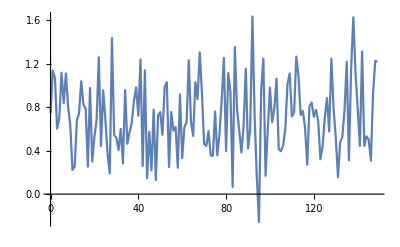

-Graphics-

```mathematica
optimalinputs[ic];

(*this is for scalar u. Make changes for other cases.*)
uopt1=Table[Uopt[[i]][[1]],{i,T}]; (*converts inputs from matrix to list for scalar u*)
xcoorinput=Range[0,T-1];
inputplotpoints=Transpose[{xcoorinput,uopt1}];
ListPlot[inputplotpoints, PlotRange->All, Joined->True,Method->"Spline"]

(*output=Cm.x+Dm.u. This is for 2D state vector. Make changes for other cases.*)
output=Table[Xopt[[i]][[1]],{i,T+1}];(*list of y=output*)
xcooroutput=Range[0,T];
outputplotpoints=Transpose[{xcooroutput,output}];
ListPlot[outputplotpoints ,Joined->True, Method->"Spline",PlotRange-> All]
```

```mathematica
uopt1
```

{0.832196}

```mathematica
x1=Table[Xopt[[i]][[1]],{i,T+1}];
x2=Table[Xopt[[i]][[2]],{i,T+1}];
phaseplanepoints=Transpose[{x1,x2}];
ListPlot[phaseplanepoints, PlotRange->All, Joined->True, Method->"Spline"]
```

-Graphics-

```mathematica
x3=Table[Xopt[[i]][[3]],{i,T+1}];
x4=Table[Xopt[[i]][[4]],{i,T+1}];
phaseplanepointsV2=Transpose[{x3,x4}];
ListPlot[phaseplanepointsV2, PlotRange->All, Joined->True, Method->"Spline"]
```

-Graphics-

```mathematica
name="PredHor10_SimHor200_FreqCons_properXposCons"<>DateString[Riffle[{"Day","Time"},"-"]]<>".mx"
DumpSave[name,{xcoorinput,xcooroutput,Xopt,Uopt}];
```

PredHor10_SimHor250_FreqCons_onlyXpos27-23:47:19.mx

```mathematica
x3s=Table[Xopt[[i]][[3]],{i,240,T+1}];
x4s=Table[Xopt[[i]][[4]],{i,240,T+1}];
phaseplanepointsV2=Transpose[{x3s,x4s}];
ListPlot[phaseplanepointsV2, PlotRange->All, Joined->True, Method->"Spline"]
```

-Graphics-